We want to examine the polynomial approximation of the sign function given in Low’s PhD thesis. This uses lemmas 6.19-6.27, functions will be named accordingly. We assume access to ϵ, Δ, and shift a for the shifted sign function Θ(x-a), or the rectangle function Rect(x/2a). We begin with a template for an approximation of the error function, and its truncation degree corresponding to an ϵ bound.

```mathematica
ntemp[β_, ϵ_]:=Ceiling[Sqrt[2*Log[4/ϵ]]*Sqrt[Ceiling[Max[β*ⅇ^2, Log[2/ϵ]]]]];
ktemp[κ_, ϵ_]:=Sqrt[2]/κ*Sqrt[Log[8/π/ϵ^2]];
ferftemp[x_, k_, n_]:=2*k*ⅇ^(-k^2/2)/Sqrt[π]*(Sum[(-1)^j*(BesselI[j, k^2/2]+BesselI[j+1, k^2/2])/(2*j+1)*ChebyshevT[2*j+1, x], {j, 0, (n-3)/2}]+(-1)^((n-1)/2)*BesselI[(n-1)/2, k^2/2]/n*ChebyshevT[n, x]);
```

```mathematica
ferf[x_, k_,ϵ_]:=ferftemp[x, k, ϵ, 2*ntemp[k^2/2, ϵ/4/k*Sqrt[π]]+1];
fl16[x_, a_,κ_, ϵ_]:=ferftemp[(x-a)/2, 2*ktemp[κ, ϵ],  2*ntemp[2*ktemp[κ, ϵ]^2,Sqrt[π]* ϵ/16/ktemp[κ, ϵ]]+1];
fgslw29rect[x_, t_, δ_, ϵ_]:=(fl16[x,t+δ/4 ,δ/2, ϵ]-fl16[x, t+δ/4,δ/2, ϵ])/2 ;
```

```mathematica
ka1=0.2;
e1=10^(-3);
a1=0.5;
delt1=0.2;
```

```mathematica
Plot[{ferftemp[x, ka1, 2*ntemp[ka1^2/2, e1/8/ka1*Sqrt[π]]-1]- Erf[ka1*x]}, {x, -1, 1}, PlotRange->Full]
(*GridLines->{{-k[0.3, 10^(-5)]/2,0,  k[0.3, 10^(-5)]/2}, {-1+10^(-5), 1-10^(-5)}}*)
```

The erf approximation works over the full range, as expected . Whereas the sign function relies on an Erf based approximation whose validity is restricted to a subset of [-1, 1], determined by k.

General::munfl: Exp[-1475.02] is too small to represent as a normalized machine number; precision may be lost.

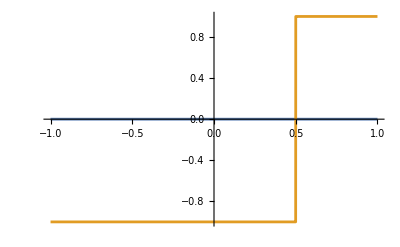

```mathematica
Plot[{fl16[x, a1, ka1, e1]-fl16[x, -a1, ka1, e1], Sign[x-a1]}, {x, -1, 1}, PlotRange->Full, GridLines->{{a1-ka1/2, a1+ka1/2}, {e1-1, 1-e1}}]
```

The plot above shows exactly the expected behaviour: a good approximation outside of the  (a-κ/2, a+κ/2) domain. Now we will try to approximate the rectangle function, following Gilyen et al.

General::munfl: Exp[-2215.95] is too small to represent as a normalized machine number; precision may be lost.

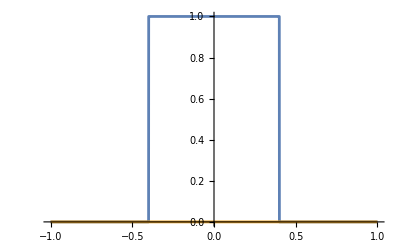

```mathematica
Plot[{(-Sign[x-a1]+Sign[x+a1])/2, fgslw29rect[x, a1, delt1, e1]}, {x,-1, 1}, PlotRange->Full, GridLines->{{-a1-delt1,-a1+delt1, a1-delt1, a1+delt1}, {e1, 1-e1, 1+e1}}]
```

Well, bright side, the sign function looks perfect, problem is that really the rectangle function problem might be inherited?? (seems unlikely based on the plots though?). In the meantime, extract the complex sign function coefficients

```mathematica
Simplify[fl16[x, a1,ka1, e1]]
```

```mathematica
F2sign:=Simplify[(fl16[x, a1,ka1, e1]+fl16[x, -a1,ka1, e1])/2/.x->(z+z^(-1))/2];
nsign=2*ntemp[2*ktemp[ka1, e1]^2,Sqrt[π]* e1/8/ktemp[ka1, e1]]+1
LaurentList=N[CoefficientList[Simplify[z^nsign*F2sign], {z}]]
```

703

CoefficientList::poly: 7.99519 Power[10, -284] <<1>> (-9.70062 Power[10, 283] + <<363>> - 7.06756 Power[10, 237] (144.6 + <<362>> + 1.13314 Power[10, -218] Power[-0.8 + <<1>> + z, 723])) is not a polynomial.

{-1.04933×10^-228-(6.40297×10^-264)/z^20+(3.70348×10^-261)/z^19-(1.05561×10^-258)/z^18+(1.97595×10^-256)/z^17-(2.73111×10^-254)/z^16+(2.97138×10^-252)/z^15-(2.64893×10^-250)/z^14+(1.98878×10^-248)/z^13-(1.28266×10^-246)/z^12+(7.21238×10^-245)/z^11-(3.57635×10^-243)/z^10+(1.57779×10^-241)/z^9-(6.23635×10^-240)/z^8+(2.22041×10^-238)/z^7-(7.15058×10^-237)/z^6+(2.08898×10^-235)/z^5-(5.54632×10^-234)/z^4+(1.33916×10^-232)/z^3-(2.93848×10^-231)/z^2+(5.84571×10^-230)/z,1.68521×10^-227,-2.38486×10^-226,2.88801×10^-225,-2.79723×10^-224,1.71569×10^-223,4.87022×10^-223,-3.38473×10^-221,5.89689×10^-220,-6.60378×10^-219,4.49721×10^-218,1.66927×10^-218,-5.52575×10^-216,8.77734×10^-215,-7.75502×10^-214,2.52084×10^-213,4.23123×10^-212,-8.57018×10^-211,7.83732×10^-210,-2.55412×10^-209,-3.79385×10^-208,7.12341×10^-207,-5.59854×10^-206,8.00581×10^-206,3.64544×10^-204,-4.84971×10^-203,2.61355×10^-202,8.15397×10^-202,-2.80962×10^-200,2.36537×10^-199,-4.1001×10^-199,-1.28535×10^-197,1.38338×10^-196,-7.94404×10^-196,-6.75543×10^-196,9.41064×10^-194,2.27313×10^-194,-3.15019×10^-192,7.55994×10^-192,8.48747×10^-190,6.61626×10^-191,-2.58834×10^-187,9.09467×10^-186,-2.46178×10^-184,-4.0821×10^-184,5.24702×10^-182,-1.54136×10^-181,-1.68956×10^-180,5.09684×10^-179,-1.01147×10^-177,-1.34404×10^-176,-9.33623×10^-176,-1.0829×10^-174,-1.96659×10^-173,-2.13048×10^-172,5.57261×10^-171,-3.675×10^-170,-1.4513×10^-169,3.74595×10^-167,2.04111×10^-167,-1.86732×10^-165,-1.55018×10^-164,-1.0308×10^-162,2.88192×10^-162,-4.78459×10^-161,2.09064×10^-160,7.00449×10^-160,2.38025×10^-159,-9.95658×10^-157,2.75579×10^-155,1.3549×10^-154,-9.44232×10^-154,-1.2501×10^-152,1.08121×10^-151,1.11056×10^-150,1.47222×10^-149,8.86906×10^-150,3.58069×10^-148,6.74434×10^-147,-5.21711×10^-145,-2.34545×10^-144,-5.0025×10^-143,-6.36569×10^-142,4.33218×10^-141,2.59202×10^-140,-2.95101×10^-139,-7.77247×10^-138,-2.95083×10^-137,-1.29582×10^-136,3.62794×10^-135,3.68015×10^-134,-3.10557×10^-133,8.96924×10^-132,5.61953×10^-131,6.0284×10^-130,-4.72933×10^-129,1.47378×10^-128,-1.34067×10^-127,4.5335×10^-126,-9.70103×10^-126,-2.06186×10^-124,4.49162×10^-123,2.01309×10^-122,-1.50398×10^-121,2.27273×10^-120,6.4878×10^-120,4.2305×10^-119,3.73765×10^-118,1.0532×10^-116,1.51003×10^-115,-1.62808×10^-115,-2.24852×10^-114,-5.04071×10^-114,-5.84581×10^-112,-6.9863×10^-112,2.22938×10^-110,6.89974×10^-109,1.97967×10^-108,8.50466×10^-108,1.40579×10^-106,-1.346×10^-105,-1.18618×10^-104,-3.76762×10^-104,1.00065×10^-102,-9.09081×10^-103,-3.48169×10^-101,7.70411×10^-101,3.27352×10^-100,-2.59253×10^-99,-9.22212×10^-98,-4.67127×10^-97,-1.06326×10^-96,3.55483×10^-95,1.75882×10^-94,7.90675×10^-94,-2.10139×10^-92,5.6585×10^-93,-1.58605×10^-91,4.0132×10^-90,-5.08255×10^-89,9.39856×10^-89,-4.95325×10^-87,3.43015×10^-86,6.93367×10^-86,1.28711×10^-84,1.77444×10^-83,-8.15533×10^-83,-3.69149×10^-84,-7.52283×10^-82,-2.11133×10^-80,2.7828×10^-79,9.44021×10^-80,4.49465×10^-78,6.06301×10^-78,-1.53602×10^-76,2.77702×10^-75,5.5853×10^-75,-1.59297×10^-75,-1.0011×10^-74,-5.46319×10^-72,9.34244×10^-73,-1.74523×10^-70,1.40389×10^-69,-5.83908×10^-70,-3.05686×10^-68,-4.21951×10^-67,-9.32009×10^-67,1.72365×10^-65,-9.28384×10^-65,-2.84227×10^-64,1.06778×10^-63,-7.1006×10^-63,-1.11435×10^-61,-1.11097×10^-61,1.61361×10^-60,2.80769×10^-59,8.47475×10^-59,8.40563×10^-58,1.24363×10^-57,3.3842×10^-56,-1.15411×10^-56,-9.43006×10^-55,1.63816×10^-54,-6.72034×10^-54,-1.96544×10^-52,3.06216×10^-51,-2.93821×10^-51,9.07419×10^-50,8.80089×10^-50,2.36303×10^-49,-1.00965×10^-47,-3.44485×10^-47,-1.43445×10^-46,3.24668×10^-46,-3.1351×10^-46,3.30484×10^-45,-3.16758×10^-43,8.00396×10^-43,-4.14584×10^-42,1.27916×10^-41,4.34558×10^-41,-1.58671×10^-39,-5.64398×10^-39,1.8828×10^-38,-1.676×10^-37,5.73143×10^-37,8.76071×10^-36,7.91273×10^-36,-2.44128×10^-35,1.48218×10^-33,-1.91042×10^-33,5.91071×10^-32,-1.17128×10^-31,3.57368×10^-31,5.1832×10^-31,-2.57935×10^-30,-7.87252×10^-29,6.22955×10^-28,3.04152×10^-27,-1.98001×10^-26,2.1619×10^-26,-1.16264×10^-25,7.02437×10^-25,1.20194×10^-23,1.09677×10^-23,2.62287×10^-22,-6.68818×10^-22,-3.93937×10^-21,-3.34476×10^-21,1.24844×10^-19,1.34263×10^-19,2.89719×10^-19,1.58647×10^-17,-3.43813×10^-17,-3.02817×10^-17,1.46755×10^-15,5.67689×10^-15,-1.8459×10^-14,3.92918×10^-14,-1.35052×10^-13,1.11531×10^-12,-4.7651×10^-12,3.06201×10^-12,-2.64898×10^-10,1.43229×10^-9,1.77783×10^-9,-3.28545×10^-8,1.25863×10^-7,-1.63057×10^-7,3.93943×10^-6,-9.44658×10^-6,0.0000132663,-0.000585991,0.0000326108,0.00378458,-0.0151402,0.00473592,0.0495207,0.948375,-23.2953,7.17032,-168.267,-846.581,213.791,-484.964,-67281.9,-118674.,-192630.,-1.55777×10^6,-2.06838×10^7,-3.17835×10^7,3.32418×10^8,-4.08124×10^8,-6.28977×10^9,1.19061×10^10,6.20613×10^10,3.4035×10^11,7.7195×10^11,-1.60093×10^12,-3.28677×10^12,-6.50423×10^13,-3.61448×10^14,3.91062×10^14,-5.65164×10^15,7.83543×10^15,-7.28627×10^16,2.72133×10^17,-5.48981×10^16,-4.78185×10^18,-1.44207×10^19,1.0559×10^20,-4.39915×10^20,7.29317×10^20,-1.11223×10^21,6.70583×10^21,-9.77716×10^21,-3.08812×10^23,-5.29043×10^23,8.34981×10^23,5.18734×10^24,-1.70013×10^24,-2.94743×10^26,-6.83555×10^26,-1.87836×10^27,5.18691×10^27,6.82056×10^28,9.85366×10^28,6.44747×10^28,7.78973×10^29,-6.39493×10^29,6.80538×10^30,6.99636×10^31,2.10364×10^32,2.9365×10^32,-1.63186×10^32,-4.40258×10^33,4.18486×10^33,1.17913×10^35,2.69766×10^35,4.48229×10^35,8.16122×10^36,2.52062×10^36,-5.9225×10^37,4.77402×10^38,-1.90173×10^39,1.51222×10^38,-2.36538×10^40,-4.90362×10^39,-1.18564×10^41,-7.39737×10^41,-1.23913×10^41,-4.44013×10^42,-5.26984×10^43,-3.66031×10^42,-1.68032×10^44,-1.86767×10^45,1.43523×10^45,-5.85751×10^45,-6.29829×10^45,-1.5612×10^47,-1.38331×10^47,1.54796×10^47,-3.3205×10^48,4.28935×10^49,-6.81416×10^48,9.64506×10^49,6.63392×10^49,1.34947×10^50,5.91703×10^51,1.39232×10^52,4.89798×10^52,4.80919×10^52,-7.626×10^52,1.34655×10^54,-1.50171×10^54,5.01709×10^54,1.76284×10^55,-3.33761×10^55,5.65048×10^56,-5.10221×10^56,9.83666×10^56,9.94734×10^57,5.95179×10^57,-1.05666×10^59,-3.81527×10^59,-3.79668×10^59,-1.02041×10^60,-3.6841×10^60,1.36217×10^61,9.05739×10^60,-6.12507×10^61,-6.14502×10^62,2.78435×10^63,-3.0837×10^63,2.08039×10^64,-2.84986×10^64,-4.23645×10^64,-1.65662×10^64,-4.66527×10^65,-1.75028×10^65,-3.93057×10^65,9.74112×10^66,1.11621×10^68,9.06514×10^67,-3.50296×10^68,1.64609×10^69,9.29943×10^69,-2.01794×10^70,-3.85006×10^70,1.67866×10^71,-8.38806×10^71,-3.51992×10^69,-1.57041×10^72,1.53813×10^73,-1.36781×10^73,7.90299×10^73,1.74755×10^74,3.14893×10^73,1.18077×10^75,-1.26614×10^75,1.07114×10^76,-4.14675×10^76,6.81579×10^74,-1.67467×10^76,-9.76145×10^77,9.34445×10^77,2.18526×10^78,8.66207×10^78,-3.82683×10^79,-8.80134×10^79,-4.69432×10^79,-2.25128×10^80,8.2686×10^80,-3.71964×10^81,1.53517×10^81,-1.69207×10^82,3.88151×10^82,1.37386×10^83,3.79961×10^83,-3.72367×10^83,4.54309×10^83,-1.28618×10^84,2.31714×10^85,4.62059×10^84,-4.35055×10^84,1.7279×10^86,9.39238×10^86,-1.31211×10^87,1.36245×10^86,-2.03127×10^88,4.088×10^88,-3.12186×10^88,-9.31575×10^88,3.73104×10^89,6.65974×10^87,1.37245×10^90,-3.49742×10^89,3.02696×10^91,-8.52439×10^90,1.50443×10^91,1.56882×10^92,1.60941×10^92,-4.44415×10^91,6.99231×10^92,-1.11799×10^92,-1.07891×10^93,-2.94277×10^94,-3.62226×10^94,-3.45599×10^94,2.87717×10^95,9.35959×10^94,-6.94137×10^95,5.10361×10^96,-7.00756×10^96,-3.04703×10^97,5.26638×10^97,3.63247×10^97,2.56661×10^98,-5.42098×10^98,6.74934×10^98,-5.08747×10^99,5.17631×10^99,-1.24985×10^100,-2.76143×10^99,-1.44301×10^100,-2.3107×10^101,4.48309×10^101,4.93191×10^100,1.91578×10^102,9.44401×10^101,1.15086×10^103,3.22443×10^103,-7.51337×10^102,-4.91484×10^103,3.09445×10^104,3.71767×10^104,-3.73438×10^104,7.18824×10^104,1.73562×10^105,2.05123×10^105,7.45376×10^105,3.45968×10^106,-1.59129×10^106,-1.54474×10^107,-1.8587×10^107,-1.35183×10^107,9.45199×10^107,1.42126×10^108,3.50987×10^108,6.64717×10^108,-4.85038×10^107,-1.85409×10^109,2.91438×10^109,1.43088×10^110,-3.32216×10^110,7.26494×10^110,6.53735×10^110,-4.62277×10^111,-2.62484×10^111,-1.29254×10^110,-1.55412×10^112,-1.40903×10^112,-1.05766×10^113,-6.21225×10^112,9.11164×10^112,2.20618×10^113,-1.45142×10^114,3.05786×10^114,-4.52456×10^114,1.05159×10^115,-3.51331×10^115,-4.08234×10^114,1.42198×10^115,-5.52105×10^114,-1.71666×10^116,9.58992×10^115,-7.66265×10^116,-1.25312×10^117,-1.49072×10^117,5.0743×10^117,3.0569×10^117,-5.52073×10^117,2.02443×10^118,6.43353×10^118,-8.39857×10^118,2.23509×10^118,-2.92703×10^119,8.35128×10^119,1.58927×10^119,-1.30601×10^120,-1.4248×10^120,-2.87394×10^120,1.18351×10^121,3.17499×10^121,-5.22598×10^121,-8.24203×10^121,-8.57963×10^121,-5.29954×10^121,-2.69872×10^122,-3.35408×10^122,-1.73787×10^123,-1.17419×10^123,2.1389×10^123,7.65902×10^123,-2.43624×10^124,1.52282×10^124,-3.93606×10^123,-9.20338×10^124,1.3052×10^125,-4.09553×10^124,1.18781×10^125,1.45094×10^125,-7.36599×10^123,2.38281×10^125,1.39843×10^125,3.02711×10^125,-4.54847×10^125,9.00362×10^125,4.15411×10^126,3.22466×10^127,-1.61733×10^127,2.32275×10^127,8.72456×10^127,8.10712×10^124,-6.9689×10^127,5.58691×10^127,1.98488×10^126,2.66639×10^128,-5.90872×10^128,2.57473×10^129,-3.71762×10^129,1.38658×10^129,-2.23005×10^129,6.07595×10^128,-1.81027×10^130,3.19955×10^130,9.51477×10^129,2.73168×10^130,-7.8343×10^130,4.0413×10^130,2.54442×10^131,1.69782×10^131,-1.38246×10^131,9.02915×10^131,-2.13369×10^131,5.68347×10^131,-1.43764×10^132,6.90063×10^131,-3.2383×10^132,-6.2352×10^132,1.53868×10^133,5.66998×10^132,-2.35077×10^133,-1.03892×10^133,-4.37366×10^133,-1.4688×10^132,-1.78766×10^134,4.37725×10^131,1.87974×10^133,1.75658×10^134,2.95834×10^134,5.89277×10^134,-5.16592×10^134,3.28196×10^134,1.66219×10^134,-1.18178×10^135,-3.42069×10^135,-2.024×10^135,4.2043×10^134,1.22446×10^136,1.91106×10^136,-6.24722×10^135,-3.61187×10^136,2.49591×10^136,2.94285×10^136,-5.48414×10^135,-5.55966×10^135,-4.055×10^136,-1.02833×10^137,-1.71167×10^137,-4.46458×10^137,-8.72707×10^136,-3.53758×10^137,3.65244×10^136,-5.43737×10^137,-3.61859×10^136,-6.54571×10^137,2.86373×10^138,1.82105×10^137,2.3455×10^138,4.66091×10^137,1.69819×10^138,-1.87982×10^138,5.71054×10^138,3.96164×10^138,-1.06004×10^139,1.67915×10^139,-2.16×10^138,1.17519×10^139,-3.60977×10^139,-3.38744×10^139,2.91456×10^139,-2.88036×10^139,9.39171×10^138,1.60649×10^139,-7.91743×10^138,-1.01599×10^140,9.13502×10^139,-1.03667×10^140,3.90969×10^140,1.5154×10^140,-1.58618×10^140,8.20934×10^140,-1.70421×10^140,-6.99067×10^140,-5.40457×10^140,4.26003×10^140,-2.03061×10^140,8.00668×10^140,-3.88662×10^140,1.25801×10^140,1.33633×10^140,-2.89488×10^141,7.12602×10^140,-2.89876×10^140,-3.99159×10^140,-3.33053×10^141,-9.99825×10^140,-4.48861×10^140,-5.00327×10^140,-3.93124×10^141,1.7255×10^141,8.90375×10^141,2.93843×10^141,7.58937×10^140,6.66696×10^139,-1.81824×10^141,7.1204×10^140,-3.50247×10^141,-9.73024×10^141,1.19013×10^142,1.39952×10^141,-2.03264×10^141,1.29179×10^142,-8.1393×10^141,8.55996×10^141,1.45534×10^142,-1.34737×10^142,-8.50325×10^141,-1.6719×10^142,1.826×10^141,-3.05249×10^142,-3.19387×10^142,1.86229×10^142,4.51797×10^142,-2.04532×10^142,-5.56811×10^141,8.74839×10^141,6.21825×10^140,1.13087×10^142,-3.24478×10^142,-3.28559×10^141,-2.60035×10^139,-1.02394×10^142,1.93207×10^141,-3.54672×10^141,-2.68028×10^142,1.36578×10^142,-8.36682×10^141,1.22935×10^141,-3.88471×10^141,-2.77708×10^142,5.1535×10^142,2.14813×10^142,-2.45751×10^142,-3.41167×10^142,5.74876×10^141,-1.45206×10^142,-3.12839×10^141,-1.58077×10^142,1.54945×10^142,9.87805×10^140,-6.86463×10^141,1.29618×10^142,-1.01756×10^142,3.27338×10^141,4.03851×10^141,-6.77931×10^141,-5.06532×10^140,4.4804×10^141,-1.39663×10^141,-1.23308×10^140,1.82651×10^141,4.31799×10^141,9.60705×10^141,2.10131×10^141,-2.36658×10^141,1.28988×10^141,-1.13861×10^141,-1.35046×10^140,-1.35283×10^141,-8.14487×10^140,1.2126×10^141,-6.00707×10^140,-3.02171×10^141,-5.12784×10^140,6.44842×10^140,-7.43351×10^140,6.72223×10^140,-6.38008×10^140,6.30553×10^140,-5.97182×10^140,-6.97701×10^140,-1.12099×10^140,6.13706×10^140,-1.58047×10^140,1.16358×10^140,3.53114×10^140,-4.17201×10^139,8.7296×10^139,-1.0252×10^140,-8.86843×10^138,1.8884×10^139,-3.60915×10^138,-3.64276×10^138,2.2995×10^139,-1.75938×10^139,-2.4393×10^139,1.32414×10^138,1.34073×10^138,2.01856×10^139,-1.31984×10^139,5.86942×10^138,7.48318×10^138,-1.30847×10^138,1.57848×10^138,2.5568×10^137,2.82918×10^138,4.95142×10^136,2.81047×10^138,2.21071×10^137,-1.90049×10^137,1.32775×10^137,7.56904×10^136,-1.54362×10^137,-6.87181×10^136,-3.7934×10^137,-1.82432×10^137,4.24609×10^136,-4.7398×10^136,2.33423×10^136,-4.37691×10^136,5.10635×10^136,1.36398×10^136,-2.99923×10^136,5.49831×10^135,2.5939×10^136,9.16009×10^135,2.54281×10^135,-1.0974×10^135,-2.78705×10^135,-2.48313×10^135,-3.21655×10^134,-6.72348×10^133,-6.6177×10^134,5.53716×10^134,2.98171×10^134,9.01278×10^133,5.42985×10^133,1.75869×10^133,-9.31897×10^133,4.68984×10^133,-5.99727×10^133,-2.54052×10^133,-1.31951×10^133,-1.14312×10^132,3.38069×10^132,-7.10625×10^132,6.28151×10^131,3.40904×10^132,-8.0349×10^131,3.0898×10^131,3.66752×10^131,4.22797×10^131,-1.31947×10^131,5.7063×10^130,9.47873×10^130,4.79576×10^130,-8.76593×10^130,1.14459×10^130,-9.99947×10^129,2.89556×10^130,-1.92098×10^130,-1.01343×10^129,2.51998×10^129,5.92691×10^128,-3.03289×10^129,1.32042×10^129,-1.81624×10^128,1.70027×10^127,4.15283×10^127,-9.64082×10^127,-1.13189×10^127,1.30586×10^125,8.19135×10^127,1.41189×10^127,-1.85111×10^127,2.88446×10^127,-7.24271×10^126,4.90777×10^126,-1.60285×10^126,1.46776×10^126,1.58041×10^126,-8.24671×10^125,2.87387×10^125,1.36248×10^125,1.17799×10^125,-2.52059×10^124,1.16199×10^125,-4.45753×10^124,6.53569×10^123,2.46387×10^124,-1.90834×10^124,8.78342×10^123,8.44241×10^122,-4.36719×10^122,-1.59973×10^123,-4.91323×10^122,-1.36002×10^122,-4.27014×10^121,-6.71274×10^121,-7.78215×10^121,-2.68185×10^121,3.56814×10^121,1.14536×10^121,-2.97058×10^120,3.29705×10^119,-2.75818×10^120,-7.8737×10^117,3.13435×10^119,-6.58346×10^117,3.63237×10^118,-4.8686×10^118,4.53126×10^118,2.93747×10^118,-8.59394×10^117,7.51108×10^117,4.36368×10^117,-8.31739×10^116,-6.09183×10^115,-3.19215×10^116,6.88941×10^115,-1.82561×10^116,4.64465×10^115,4.16048×10^115,-1.84516×10^114,-2.77817×10^115,2.06787×10^114,-1.87592×10^114,4.50298×10^114,-1.02545×10^114,6.95887×10^113,-1.70607×10^112,-4.38228×10^112,-7.8448×10^112,1.41865×10^112,-1.21086×10^112,-5.6956×10^111,-1.13251×10^111,-2.23103×10^111,5.79131×10^110,3.07282×10^110,-3.74586×10^109,-2.18093×10^109,3.99197×10^109,-2.08071×10^109,1.5734×10^109,4.24087×10^108,4.1552×10^108,3.78677×10^107,5.99995×10^107,-3.60332×10^107,-1.39997×10^107,-4.11188×10^106,2.79626×10^106,6.22552×10^104,1.03748×10^106,-1.16891×10^105,3.00632×10^105,6.72697×10^104,-1.40313×10^105,4.58922×10^104,3.53714×10^104,-1.18203×10^103,-3.14496×10^103,2.45535×10^103,8.13379×10^102,1.14164×10^102,6.46295×10^101,-2.88898×10^101,4.91797×10^101,-2.10043×10^101,3.83742×10^100,8.47691×10^99,5.11728×10^99,-9.51165×10^98,-3.36742×10^99,1.53115×10^99,-8.88836×10^98,1.06947×10^98,3.53234×10^97,2.61736×10^97,-1.53508×10^97,-1.29923×10^97,1.36793×10^96,1.27207×10^96,4.57444×10^95,2.09899×10^95,-7.31074×10^94,-2.46887×10^94,-6.64734×10^91,5.54314×10^93,3.02808×10^93,9.01277×10^92,1.63208×10^92,5.49961×10^92,3.57144×10^91,6.83127×10^91,-7.46736×10^90,3.63161×10^91,-2.50322×10^90,1.9378×10^89,-4.92691×10^89,2.02134×10^89,-1.83531×10^87,-1.6334×10^88,5.09748×10^88,-1.05412×10^88,-1.09787×10^87,8.2579×10^85,8.1301×10^86,2.70405×10^86,-3.18936×10^85,-1.84189×10^85,5.26048×10^84,-4.45436×10^84,-1.37624×10^83,1.71919×10^83,4.28789×10^83,1.76897×10^83,5.45086×10^82,-1.11834×10^82,6.57598×10^81,-2.69719×10^81,2.53639×10^81,-3.54916×10^80,-4.51835×10^79,-1.04188×10^80,-1.31619×10^79,1.31631×10^79,1.30565×10^78,1.37999×10^78,-9.9071×10^77,4.62655×10^75,-5.69711×10^76,-3.93961×10^76,7.84595×10^75,-4.56381×10^75,1.66672×10^75,3.10349×10^73,2.2729×10^74,1.07689×10^74,-9.13315×10^72,1.62451×10^73,-4.08743×10^72,-2.21227×10^71,-7.435×10^71,2.36758×10^71,-1.79081×10^70,-2.51051×10^70,1.08537×10^70,1.20235×10^69,-2.76236×10^68,1.06008×10^68,1.45059×10^68,-8.19664×10^66,-3.23066×10^66,-3.89625×10^66,-1.00818×10^66,3.71469×10^64,7.66186×10^64,1.10816×10^64,1.54766×10^64,-8.55418×10^63,2.71351×10^63,6.88692×10^61,2.4711×10^62,4.2546×10^61,-1.39307×10^60,4.46214×10^59,-3.02122×10^60,4.2524×10^59,-3.26298×10^59,-3.89821×10^58,5.73289×10^57,1.25834×10^58,2.59992×10^57,5.23378×10^56,1.24137×10^56,8.0324×10^54,-6.71215×10^54,1.5092×10^55,-6.70338×10^54,2.21409×10^54,-6.63054×10^52,1.85631×10^52,1.49675×10^51,1.99032×10^52,5.32294×10^51,9.35117×10^50,-3.6592×10^49,1.06539×10^50,-2.26664×10^48,3.61427×10^49,-5.17125×10^48,1.1489×10^48,-2.57062×10^46,-2.2561×10^47,2.99165×10^45,-2.08564×10^45,1.79992×10^45,-1.76881×10^45,-1.6648×10^44,2.18064×10^43,-4.26143×10^43,-4.63389×10^41,-4.71847×10^41,-6.97336×10^41,-7.56004×10^40,-2.11648×10^39,-2.52523×10^40,-5.15227×10^38,-8.10578×10^38,1.30705×10^38,-5.56063×10^37,-1.31557×10^37,1.06691×10^36,5.9649×10^35,2.39886×10^35,1.31576×10^35,2.26182×10^34,-3.35311×10^33,7.84634×10^32,3.54087×10^32,5.40289×10^31,2.87113×10^31,1.54464×10^31,-3.75504×10^29,1.34305×10^30,1.20985×10^29,1.86089×10^29,6.3536×10^28,5.44918×10^27,-2.83659×10^27,-5.43178×10^26,-2.99853×10^26,-5.10942×10^24,1.04304×10^25,9.72371×10^23,-7.09518×10^22,-3.03182×10^23,-7.74497×10^21,1.50979×10^22,-7.92351×10^19,-6.11913×10^20,-4.73624×10^20,4.12374×10^19,-2.27038×10^19,-4.30718×10^18,7.10771×10^17,4.02982×10^17,-5.78845×10^16,1.78732×10^15,-4.95893×10^15,5.30596×10^14,-3.70451×10^14,-6.09819×10^13,-1.76582×10^13,-2.1239×10^11,1.52016×10^12,2.73945×10^11,7.60322×10^10,-2.34586×10^8,-7.15177×10^9,-9.04346×10^7,3.86731×10^8,-5.45721×10^7,-2.27621×10^7,-894340.,-586264.,-29963.2,-56201.5,104.008,2084.46,-599.642,-103.739,2.51326,-22.8612,-0.535962,0.0257115,0.0145246,0.00316145,0.00146826,0.000908037,-0.000358461,6.83027×10^-6,-4.2399×10^-6,3.78166×10^-6,2.65788×10^-7,1.35104×10^-7,-4.3443×10^-8,3.36035×10^-9,7.32913×10^-10,-2.23982×10^-10,-3.26566×10^-11,1.01027×10^-11,9.63654×10^-13,-1.43801×10^-13,-1.00487×10^-13,-2.84353×10^-14,5.37161×10^-15,3.37199×10^-16,-1.23796×10^-16,1.22937×10^-17,1.54647×10^-17,1.17819×10^-19,6.01041×10^-21,1.75933×10^-19,-1.50805×10^-20,-1.87358×10^-21,-6.39257×10^-22,3.07058×10^-22,-1.16986×10^-23,1.29181×10^-23,9.70707×10^-26,1.80454×10^-25,-3.3343×10^-26,-1.75249×10^-26,3.40839×10^-27,3.57981×10^-28,-2.0887×10^-29,8.90532×10^-30,-1.51449×10^-30,4.03095×10^-31,-9.70364×10^-32,5.03839×10^-32,-4.01708×10^-33,1.4045×10^-33,-1.61429×10^-34,1.34696×10^-35,3.98751×10^-36,5.95102×10^-37,-2.51751×10^-37,2.43249×10^-38,-4.72843×10^-39,-1.35149×10^-39,-3.38395×10^-41,4.39781×10^-41,-5.00393×10^-42,2.26114×10^-43,-1.75603×10^-43,-2.85723×10^-44,-5.30474×10^-45,1.54077×10^-45,-2.40109×10^-46,-2.9107×10^-47,5.1687×10^-49,1.39451×10^-48,1.00811×10^-49,4.48626×10^-50,-1.66731×10^-51,3.44263×10^-51,-1.14046×10^-52,-1.36498×10^-53,8.60863×10^-55,-1.88707×10^-54,1.03192×10^-55,1.76984×10^-56,1.68267×10^-57,6.14097×10^-58,4.29924×10^-59,1.29801×10^-59,2.03666×10^-60,-3.19535×10^-62,-1.07682×10^-61,-6.02222×10^-63,-4.52433×10^-64,-4.41352×10^-64,-4.44288×10^-65,1.03032×10^-65,-5.30658×10^-68,-5.34881×10^-67,-1.37403×10^-68,-6.54309×10^-70,1.95081×10^-69,-2.24677×10^-70,1.83347×10^-71,-6.09387×10^-72,-1.54693×10^-73,6.26397×10^-74,1.72979×10^-75,1.80826×10^-75,-1.36881×10^-76,4.20888×10^-78,3.92871×10^-78,1.14967×10^-78,2.75752×10^-79,-2.67431×10^-80,-1.57045×10^-81,-4.43641×10^-84,-6.40867×10^-83,1.14348×10^-83,-3.18891×10^-85,1.2871×10^-85,1.90114×10^-86,-1.35114×10^-87,-1.23348×10^-88,-3.92411×10^-89,-2.29276×10^-90,8.07526×10^-93,-1.46534×10^-92,-1.29456×10^-92,-2.00199×10^-93,5.61637×10^-94,4.16156×10^-95,4.17223×10^-96,-1.08352×10^-96,-3.04173×10^-98,-1.1105×10^-99,-3.58799×10^-100,1.11246×10^-100,-4.17431×10^-101,-1.41377×10^-102,5.65428×10^-103,4.2767×10^-104,-1.17263×10^-104,-3.15097×10^-106,3.17077×10^-107,6.00085×10^-108,3.70081×10^-109,5.46731×10^-109,2.30924×10^-110,-2.73886×10^-111,-5.20789×10^-112,1.83764×10^-113,3.93103×10^-115,-2.24198×10^-115,1.65021×10^-115,1.18247×10^-116,1.04985×10^-117,4.09925×10^-119,1.408×10^-119,1.60733×10^-120,-1.26497×10^-121,-5.24963×10^-124,4.54791×10^-123,-4.50685×10^-124,-2.53773×10^-126,1.30435×10^-126,-8.40406×10^-128,-1.07051×10^-128,-4.68412×10^-129,3.27711×10^-130,8.80075×10^-131,5.35707×10^-132,-2.84276×10^-133,3.96274×10^-135,5.77975×10^-135,-1.81145×10^-137,-9.69226×10^-138,-8.85923×10^-138,-2.5424×10^-139,-1.93245×10^-140,5.17046×10^-141,-6.98091×10^-142,-4.57244×10^-143,5.1475×10^-144,-3.86263×10^-145,-5.03002×10^-147,-6.50795×10^-148,1.12421×10^-148,-2.47512×10^-149,-9.88691×10^-151,-1.68384×10^-151,-1.55451×10^-152,-1.83058×10^-153,1.92835×10^-154,-4.96557×10^-157,-3.01739×10^-157,4.51561×10^-158,7.26024×10^-159,1.22315×10^-160,7.72056×10^-162,2.58763×10^-162,-1.07687×10^-162,-2.89486×10^-164,-2.77757×10^-165,1.13249×10^-166,3.83549×10^-167,-1.01913×10^-169,4.6822×10^-170,7.78243×10^-172,-2.21628×10^-172,-6.59211×10^-174,-1.93604×10^-174,6.16367×10^-176,-7.88105×10^-177,-8.28315×10^-178,4.782×10^-179,1.54801×10^-180,1.33733×10^-181,5.19449×10^-182,-3.14469×10^-183,-4.58733×10^-184,9.21634×10^-186,-6.68626×10^-187,-8.97534×10^-190,8.31064×10^-190,-1.74352×10^-190,-3.38867×10^-192,3.94894×10^-193,1.39023×10^-193,-2.10181×10^-195,-7.05435×10^-196,1.41032×10^-196,-1.31833×10^-197,-4.10479×10^-199,2.35206×10^-199,-2.80944×10^-200,8.16684×10^-202,2.61362×10^-202,-4.8497×10^-203,3.64529×10^-204,8.0048×10^-206,-5.5986×10^-206,7.12352×10^-207,-3.7938×10^-208,-2.55414×10^-209,7.83733×10^-210,-8.57018×10^-211,4.23123×10^-212,2.52084×10^-213,-7.75502×10^-214,8.77734×10^-215,-5.52575×10^-216,1.66927×10^-218,4.49721×10^-218,-6.60378×10^-219,5.89689×10^-220,-3.38473×10^-221,4.87022×10^-223,1.71569×10^-223,-2.79723×10^-224,2.88801×10^-225,-2.38486×10^-226,1.68521×10^-227,-1.04933×10^-228,5.84571×10^-230,-2.93848×10^-231,1.33916×10^-232,-5.54632×10^-234,2.08898×10^-235,-7.15058×10^-237,2.22041×10^-238,-6.23635×10^-240,1.57779×10^-241,-3.57635×10^-243,7.21238×10^-245,-1.28266×10^-246,1.98878×10^-248,-2.64893×10^-250,2.97138×10^-252,-2.73111×10^-254,1.97595×10^-256,-1.05561×10^-258,3.70348×10^-261,-6.40297×10^-264}

Now partition into odd, even coeff sets: here one of these sets should be all zeros

```mathematica
A=Partition[LaurentList,2,2,1,{}]~Flatten~{2};
LeadingList=Riffle[A[[1]], 0, 2]
NonleadingList=Riffle[A[[2]], 0, {1, 2*nsign+1, 2}]
OddList=If[EvenQ[nsign]==True, NonleadingList, LeadingList];
EvenList=If[EvenQ[nsign]==True, LeadingList, NonleadingList];
```

{-1.04933×10^-228-(6.40297×10^-264)/z^20+(3.70348×10^-261)/z^19-(1.05561×10^-258)/z^18+(1.97595×10^-256)/z^17-(2.73111×10^-254)/z^16+(2.97138×10^-252)/z^15-(2.64893×10^-250)/z^14+(1.98878×10^-248)/z^13-(1.28266×10^-246)/z^12+(7.21238×10^-245)/z^11-(3.57635×10^-243)/z^10+(1.57779×10^-241)/z^9-(6.23635×10^-240)/z^8+(2.22041×10^-238)/z^7-(7.15058×10^-237)/z^6+(2.08898×10^-235)/z^5-(5.54632×10^-234)/z^4+(1.33916×10^-232)/z^3-(2.93848×10^-231)/z^2+(5.84571×10^-230)/z,0,-2.38486×10^-226,0,-2.79723×10^-224,0,4.87022×10^-223,0,5.89689×10^-220,0,4.49721×10^-218,0,-5.52575×10^-216,0,-7.75502×10^-214,0,4.23123×10^-212,0,7.83732×10^-210,0,-3.79385×10^-208,0,-5.59854×10^-206,0,3.64544×10^-204,0,2.61355×10^-202,0,-2.80962×10^-200,0,-4.1001×10^-199,0,1.38338×10^-196,0,-6.75543×10^-196,0,2.27313×10^-194,0,7.55994×10^-192,0,6.61626×10^-191,0,9.09467×10^-186,0,-4.0821×10^-184,0,-1.54136×10^-181,0,5.09684×10^-179,0,-1.34404×10^-176,0,-1.0829×10^-174,0,-2.13048×10^-172,0,-3.675×10^-170,0,3.74595×10^-167,0,-1.86732×10^-165,0,-1.0308×10^-162,0,-4.78459×10^-161,0,7.00449×10^-160,0,-9.95658×10^-157,0,1.3549×10^-154,0,-1.2501×10^-152,0,1.11056×10^-150,0,8.86906×10^-150,0,6.74434×10^-147,0,-2.34545×10^-144,0,-6.36569×10^-142,0,2.59202×10^-140,0,-7.77247×10^-138,0,-1.29582×10^-136,0,3.68015×10^-134,0,8.96924×10^-132,0,6.0284×10^-130,0,1.47378×10^-128,0,4.5335×10^-126,0,-2.06186×10^-124,0,2.01309×10^-122,0,2.27273×10^-120,0,4.2305×10^-119,0,1.0532×10^-116,0,-1.62808×10^-115,0,-5.04071×10^-114,0,-6.9863×10^-112,0,6.89974×10^-109,0,8.50466×10^-108,0,-1.346×10^-105,0,-3.76762×10^-104,0,-9.09081×10^-103,0,7.70411×10^-101,0,-2.59253×10^-99,0,-4.67127×10^-97,0,3.55483×10^-95,0,7.90675×10^-94,0,5.6585×10^-93,0,4.0132×10^-90,0,9.39856×10^-89,0,3.43015×10^-86,0,1.28711×10^-84,0,-8.15533×10^-83,0,-7.52283×10^-82,0,2.7828×10^-79,0,4.49465×10^-78,0,-1.53602×10^-76,0,5.5853×10^-75,0,-1.0011×10^-74,0,9.34244×10^-73,0,1.40389×10^-69,0,-3.05686×10^-68,0,-9.32009×10^-67,0,-9.28384×10^-65,0,1.06778×10^-63,0,-1.11435×10^-61,0,1.61361×10^-60,0,8.47475×10^-59,0,1.24363×10^-57,0,-1.15411×10^-56,0,1.63816×10^-54,0,-1.96544×10^-52,0,-2.93821×10^-51,0,8.80089×10^-50,0,-1.00965×10^-47,0,-1.43445×10^-46,0,-3.1351×10^-46,0,-3.16758×10^-43,0,-4.14584×10^-42,0,4.34558×10^-41,0,-5.64398×10^-39,0,-1.676×10^-37,0,8.76071×10^-36,0,-2.44128×10^-35,0,-1.91042×10^-33,0,-1.17128×10^-31,0,5.1832×10^-31,0,-7.87252×10^-29,0,3.04152×10^-27,0,2.1619×10^-26,0,7.02437×10^-25,0,1.09677×10^-23,0,-6.68818×10^-22,0,-3.34476×10^-21,0,1.34263×10^-19,0,1.58647×10^-17,0,-3.02817×10^-17,0,5.67689×10^-15,0,3.92918×10^-14,0,1.11531×10^-12,0,3.06201×10^-12,0,1.43229×10^-9,0,-3.28545×10^-8,0,-1.63057×10^-7,0,-9.44658×10^-6,0,-0.000585991,0,0.00378458,0,0.00473592,0,0.948375,0,7.17032,0,-846.581,0,-484.964,0,-118674.,0,-1.55777×10^6,0,-3.17835×10^7,0,-4.08124×10^8,0,1.19061×10^10,0,3.4035×10^11,0,-1.60093×10^12,0,-6.50423×10^13,0,3.91062×10^14,0,7.83543×10^15,0,2.72133×10^17,0,-4.78185×10^18,0,1.0559×10^20,0,7.29317×10^20,0,6.70583×10^21,0,-3.08812×10^23,0,8.34981×10^23,0,-1.70013×10^24,0,-6.83555×10^26,0,5.18691×10^27,0,9.85366×10^28,0,7.78973×10^29,0,6.80538×10^30,0,2.10364×10^32,0,-1.63186×10^32,0,4.18486×10^33,0,2.69766×10^35,0,8.16122×10^36,0,-5.9225×10^37,0,-1.90173×10^39,0,-2.36538×10^40,0,-1.18564×10^41,0,-1.23913×10^41,0,-5.26984×10^43,0,-1.68032×10^44,0,1.43523×10^45,0,-6.29829×10^45,0,-1.38331×10^47,0,-3.3205×10^48,0,-6.81416×10^48,0,6.63392×10^49,0,5.91703×10^51,0,4.89798×10^52,0,-7.626×10^52,0,-1.50171×10^54,0,1.76284×10^55,0,5.65048×10^56,0,9.83666×10^56,0,5.95179×10^57,0,-3.81527×10^59,0,-1.02041×10^60,0,1.36217×10^61,0,-6.12507×10^61,0,2.78435×10^63,0,2.08039×10^64,0,-4.23645×10^64,0,-4.66527×10^65,0,-3.93057×10^65,0,1.11621×10^68,0,-3.50296×10^68,0,9.29943×10^69,0,-3.85006×10^70,0,-8.38806×10^71,0,-1.57041×10^72,0,-1.36781×10^73,0,1.74755×10^74,0,1.18077×10^75,0,1.07114×10^76,0,6.81579×10^74,0,-9.76145×10^77,0,2.18526×10^78,0,-3.82683×10^79,0,-4.69432×10^79,0,8.2686×10^80,0,1.53517×10^81,0,3.88151×10^82,0,3.79961×10^83,0,4.54309×10^83,0,2.31714×10^85,0,-4.35055×10^84,0,9.39238×10^86,0,1.36245×10^86,0,4.088×10^88,0,-9.31575×10^88,0,6.65974×10^87,0,-3.49742×10^89,0,-8.52439×10^90,0,1.56882×10^92,0,-4.44415×10^91,0,-1.11799×10^92,0,-2.94277×10^94,0,-3.45599×10^94,0,9.35959×10^94,0,5.10361×10^96,0,-3.04703×10^97,0,3.63247×10^97,0,-5.42098×10^98,0,-5.08747×10^99,0,-1.24985×10^100,0,-1.44301×10^100,0,4.48309×10^101,0,1.91578×10^102,0,1.15086×10^103,0,-7.51337×10^102,0,3.09445×10^104,0,-3.73438×10^104,0,1.73562×10^105,0,7.45376×10^105,0,-1.59129×10^106,0,-1.8587×10^107,0,9.45199×10^107,0,3.50987×10^108,0,-4.85038×10^107,0,2.91438×10^109,0,-3.32216×10^110,0,6.53735×10^110,0,-2.62484×10^111,0,-1.55412×10^112,0,-1.05766×10^113,0,9.11164×10^112,0,-1.45142×10^114,0,-4.52456×10^114,0,-3.51331×10^115,0,1.42198×10^115,0,-1.71666×10^116,0,-7.66265×10^116,0,-1.49072×10^117,0,3.0569×10^117,0,2.02443×10^118,0,-8.39857×10^118,0,-2.92703×10^119,0,1.58927×10^119,0,-1.4248×10^120,0,1.18351×10^121,0,-5.22598×10^121,0,-8.57963×10^121,0,-2.69872×10^122,0,-1.73787×10^123,0,2.1389×10^123,0,-2.43624×10^124,0,-3.93606×10^123,0,1.3052×10^125,0,1.18781×10^125,0,-7.36599×10^123,0,1.39843×10^125,0,-4.54847×10^125,0,4.15411×10^126,0,-1.61733×10^127,0,8.72456×10^127,0,-6.9689×10^127,0,1.98488×10^126,0,-5.90872×10^128,0,-3.71762×10^129,0,-2.23005×10^129,0,-1.81027×10^130,0,9.51477×10^129,0,-7.8343×10^130,0,2.54442×10^131,0,-1.38246×10^131,0,-2.13369×10^131,0,-1.43764×10^132,0,-3.2383×10^132,0,1.53868×10^133,0,-2.35077×10^133,0,-4.37366×10^133,0,-1.78766×10^134,0,1.87974×10^133,0,2.95834×10^134,0,-5.16592×10^134,0,1.66219×10^134,0,-3.42069×10^135,0,4.2043×10^134,0,1.91106×10^136,0,-3.61187×10^136,0,2.94285×10^136,0,-5.55966×10^135,0,-1.02833×10^137,0,-4.46458×10^137,0,-3.53758×10^137,0,-5.43737×10^137,0,-6.54571×10^137,0,1.82105×10^137,0,4.66091×10^137,0,-1.87982×10^138,0,3.96164×10^138,0,1.67915×10^139,0,1.17519×10^139,0,-3.38744×10^139,0,-2.88036×10^139,0,1.60649×10^139,0,-1.01599×10^140,0,-1.03667×10^140,0,1.5154×10^140,0,8.20934×10^140,0,-6.99067×10^140,0,4.26003×10^140,0,8.00668×10^140,0,1.25801×10^140,0,-2.89488×10^141,0,-2.89876×10^140,0,-3.33053×10^141,0,-4.48861×10^140,0,-3.93124×10^141,0,8.90375×10^141,0,7.58937×10^140,0,-1.81824×10^141,0,-3.50247×10^141,0,1.19013×10^142,0,-2.03264×10^141,0,-8.1393×10^141,0,1.45534×10^142,0,-8.50325×10^141,0,1.826×10^141,0,-3.19387×10^142,0,4.51797×10^142,0,-5.56811×10^141,0,6.21825×10^140,0,-3.24478×10^142,0,-2.60035×10^139,0,1.93207×10^141,0,-2.68028×10^142,0,-8.36682×10^141,0,-3.88471×10^141,0,5.1535×10^142,0,-2.45751×10^142,0,5.74876×10^141,0,-3.12839×10^141,0,1.54945×10^142,0,-6.86463×10^141,0,-1.01756×10^142,0,4.03851×10^141,0,-5.06532×10^140,0,-1.39663×10^141,0,1.82651×10^141,0,9.60705×10^141,0,-2.36658×10^141,0,-1.13861×10^141,0,-1.35283×10^141,0,1.2126×10^141,0,-3.02171×10^141,0,6.44842×10^140,0,6.72223×10^140,0,6.30553×10^140,0,-6.97701×10^140,0,6.13706×10^140,0,1.16358×10^140,0,-4.17201×10^139,0,-1.0252×10^140,0,1.8884×10^139,0,-3.64276×10^138,0,-1.75938×10^139,0,1.32414×10^138,0,2.01856×10^139,0,5.86942×10^138,0,-1.30847×10^138,0,2.5568×10^137,0,4.95142×10^136,0,2.21071×10^137,0,1.32775×10^137,0,-1.54362×10^137,0,-3.7934×10^137,0,4.24609×10^136,0,2.33423×10^136,0,5.10635×10^136,0,-2.99923×10^136,0,2.5939×10^136,0,2.54281×10^135,0,-2.78705×10^135,0,-3.21655×10^134,0,-6.6177×10^134,0,2.98171×10^134,0,5.42985×10^133,0,-9.31897×10^133,0,-5.99727×10^133,0,-1.31951×10^133,0,3.38069×10^132,0,6.28151×10^131,0,-8.0349×10^131,0,3.66752×10^131,0,-1.31947×10^131,0,9.47873×10^130,0,-8.76593×10^130,0,-9.99947×10^129,0,-1.92098×10^130,0,2.51998×10^129,0,-3.03289×10^129,0,-1.81624×10^128,0,4.15283×10^127,0,-1.13189×10^127,0,8.19135×10^127,0,-1.85111×10^127,0,-7.24271×10^126,0,-1.60285×10^126,0,1.58041×10^126,0,2.87387×10^125,0,1.17799×10^125,0,1.16199×10^125,0,6.53569×10^123,0,-1.90834×10^124,0,8.44241×10^122,0,-1.59973×10^123,0,-1.36002×10^122,0,-6.71274×10^121,0,-2.68185×10^121,0,1.14536×10^121,0,3.29705×10^119,0,-7.8737×10^117,0,-6.58346×10^117,0,-4.8686×10^118,0,2.93747×10^118,0,7.51108×10^117,0,-8.31739×10^116,0,-3.19215×10^116,0,-1.82561×10^116,0,4.16048×10^115,0,-2.77817×10^115,0,-1.87592×10^114,0,-1.02545×10^114,0,-1.70607×10^112,0,-7.8448×10^112,0,-1.21086×10^112,0,-1.13251×10^111,0,5.79131×10^110,0,-3.74586×10^109,0,3.99197×10^109,0,1.5734×10^109,0,4.1552×10^108,0,5.99995×10^107,0,-1.39997×10^107,0,2.79626×10^106,0,1.03748×10^106,0,3.00632×10^105,0,-1.40313×10^105,0,3.53714×10^104,0,-3.14496×10^103,0,8.13379×10^102,0,6.46295×10^101,0,4.91797×10^101,0,3.83742×10^100,0,5.11728×10^99,0,-3.36742×10^99,0,-8.88836×10^98,0,3.53234×10^97,0,-1.53508×10^97,0,1.36793×10^96,0,4.57444×10^95,0,-7.31074×10^94,0,-6.64734×10^91,0,3.02808×10^93,0,1.63208×10^92,0,3.57144×10^91,0,-7.46736×10^90,0,-2.50322×10^90,0,-4.92691×10^89,0,-1.83531×10^87,0,5.09748×10^88,0,-1.09787×10^87,0,8.1301×10^86,0,-3.18936×10^85,0,5.26048×10^84,0,-1.37624×10^83,0,4.28789×10^83,0,5.45086×10^82,0,6.57598×10^81,0,2.53639×10^81,0,-4.51835×10^79,0,-1.31619×10^79,0,1.30565×10^78,0,-9.9071×10^77,0,-5.69711×10^76,0,7.84595×10^75,0,1.66672×10^75,0,2.2729×10^74,0,-9.13315×10^72,0,-4.08743×10^72,0,-7.435×10^71,0,-1.79081×10^70,0,1.08537×10^70,0,-2.76236×10^68,0,1.45059×10^68,0,-3.23066×10^66,0,-1.00818×10^66,0,7.66186×10^64,0,1.54766×10^64,0,2.71351×10^63,0,2.4711×10^62,0,-1.39307×10^60,0,-3.02122×10^60,0,-3.26298×10^59,0,5.73289×10^57,0,2.59992×10^57,0,1.24137×10^56,0,-6.71215×10^54,0,-6.70338×10^54,0,-6.63054×10^52,0,1.49675×10^51,0,5.32294×10^51,0,-3.6592×10^49,0,-2.26664×10^48,0,-5.17125×10^48,0,-2.57062×10^46,0,2.99165×10^45,0,1.79992×10^45,0,-1.6648×10^44,0,-4.26143×10^43,0,-4.71847×10^41,0,-7.56004×10^40,0,-2.52523×10^40,0,-8.10578×10^38,0,-5.56063×10^37,0,1.06691×10^36,0,2.39886×10^35,0,2.26182×10^34,0,7.84634×10^32,0,5.40289×10^31,0,1.54464×10^31,0,1.34305×10^30,0,1.86089×10^29,0,5.44918×10^27,0,-5.43178×10^26,0,-5.10942×10^24,0,9.72371×10^23,0,-3.03182×10^23,0,1.50979×10^22,0,-6.11913×10^20,0,4.12374×10^19,0,-4.30718×10^18,0,4.02982×10^17,0,1.78732×10^15,0,5.30596×10^14,0,-6.09819×10^13,0,-2.1239×10^11,0,2.73945×10^11,0,-2.34586×10^8,0,-9.04346×10^7,0,-5.45721×10^7,0,-894340.,0,-29963.2,0,104.008,0,-599.642,0,2.51326,0,-0.535962,0,0.0145246,0,0.00146826,0,-0.000358461,0,-4.2399×10^-6,0,2.65788×10^-7,0,-4.3443×10^-8,0,7.32913×10^-10,0,-3.26566×10^-11,0,9.63654×10^-13,0,-1.00487×10^-13,0,5.37161×10^-15,0,-1.23796×10^-16,0,1.54647×10^-17,0,6.01041×10^-21,0,-1.50805×10^-20,0,-6.39257×10^-22,0,-1.16986×10^-23,0,9.70707×10^-26,0,-3.3343×10^-26,0,3.40839×10^-27,0,-2.0887×10^-29,0,-1.51449×10^-30,0,-9.70364×10^-32,0,-4.01708×10^-33,0,-1.61429×10^-34,0,3.98751×10^-36,0,-2.51751×10^-37,0,-4.72843×10^-39,0,-3.38395×10^-41,0,-5.00393×10^-42,0,-1.75603×10^-43,0,-5.30474×10^-45,0,-2.40109×10^-46,0,5.1687×10^-49,0,1.00811×10^-49,0,-1.66731×10^-51,0,-1.14046×10^-52,0,8.60863×10^-55,0,1.03192×10^-55,0,1.68267×10^-57,0,4.29924×10^-59,0,2.03666×10^-60,0,-1.07682×10^-61,0,-4.52433×10^-64,0,-4.44288×10^-65,0,-5.30658×10^-68,0,-1.37403×10^-68,0,1.95081×10^-69,0,1.83347×10^-71,0,-1.54693×10^-73,0,1.72979×10^-75,0,-1.36881×10^-76,0,3.92871×10^-78,0,2.75752×10^-79,0,-1.57045×10^-81,0,-6.40867×10^-83,0,-3.18891×10^-85,0,1.90114×10^-86,0,-1.23348×10^-88,0,-2.29276×10^-90,0,-1.46534×10^-92,0,-2.00199×10^-93,0,4.16156×10^-95,0,-1.08352×10^-96,0,-1.1105×10^-99,0,1.11246×10^-100,0,-1.41377×10^-102,0,4.2767×10^-104,0,-3.15097×10^-106,0,6.00085×10^-108,0,5.46731×10^-109,0,-2.73886×10^-111,0,1.83764×10^-113,0,-2.24198×10^-115,0,1.18247×10^-116,0,4.09925×10^-119,0,1.60733×10^-120,0,-5.24963×10^-124,0,-4.50685×10^-124,0,1.30435×10^-126,0,-1.07051×10^-128,0,3.27711×10^-130,0,5.35707×10^-132,0,3.96274×10^-135,0,-1.81145×10^-137,0,-8.85923×10^-138,0,-1.93245×10^-140,0,-6.98091×10^-142,0,5.1475×10^-144,0,-5.03002×10^-147,0,1.12421×10^-148,0,-9.88691×10^-151,0,-1.55451×10^-152,0,1.92835×10^-154,0,-3.01739×10^-157,0,7.26024×10^-159,0,7.72056×10^-162,0,-1.07687×10^-162,0,-2.77757×10^-165,0,3.83549×10^-167,0,4.6822×10^-170,0,-2.21628×10^-172,0,-1.93604×10^-174,0,-7.88105×10^-177,0,4.782×10^-179,0,1.33733×10^-181,0,-3.14469×10^-183,0,9.21634×10^-186,0,-8.97534×10^-190,0,-1.74352×10^-190,0,3.94894×10^-193,0,-2.10181×10^-195,0,1.41032×10^-196,0,-4.10479×10^-199,0,-2.80944×10^-200,0,2.61362×10^-202,0,3.64529×10^-204,0,-5.5986×10^-206,0,-3.7938×10^-208,0,7.83733×10^-210,0,4.23123×10^-212,0,-7.75502×10^-214,0,-5.52575×10^-216,0,4.49721×10^-218,0,5.89689×10^-220,0,4.87022×10^-223,0,-2.79723×10^-224,0,-2.38486×10^-226,0,-1.04933×10^-228,0,-2.93848×10^-231,0,-5.54632×10^-234,0,-7.15058×10^-237,0,-6.23635×10^-240,0,-3.57635×10^-243,0,-1.28266×10^-246,0,-2.64893×10^-250,0,-2.73111×10^-254,0,-1.05561×10^-258,0,-6.40297×10^-264}

{0,1.68521×10^-227,0,2.88801×10^-225,0,1.71569×10^-223,0,-3.38473×10^-221,0,-6.60378×10^-219,0,1.66927×10^-218,0,8.77734×10^-215,0,2.52084×10^-213,0,-8.57018×10^-211,0,-2.55412×10^-209,0,7.12341×10^-207,0,8.00581×10^-206,0,-4.84971×10^-203,0,8.15397×10^-202,0,2.36537×10^-199,0,-1.28535×10^-197,0,-7.94404×10^-196,0,9.41064×10^-194,0,-3.15019×10^-192,0,8.48747×10^-190,0,-2.58834×10^-187,0,-2.46178×10^-184,0,5.24702×10^-182,0,-1.68956×10^-180,0,-1.01147×10^-177,0,-9.33623×10^-176,0,-1.96659×10^-173,0,5.57261×10^-171,0,-1.4513×10^-169,0,2.04111×10^-167,0,-1.55018×10^-164,0,2.88192×10^-162,0,2.09064×10^-160,0,2.38025×10^-159,0,2.75579×10^-155,0,-9.44232×10^-154,0,1.08121×10^-151,0,1.47222×10^-149,0,3.58069×10^-148,0,-5.21711×10^-145,0,-5.0025×10^-143,0,4.33218×10^-141,0,-2.95101×10^-139,0,-2.95083×10^-137,0,3.62794×10^-135,0,-3.10557×10^-133,0,5.61953×10^-131,0,-4.72933×10^-129,0,-1.34067×10^-127,0,-9.70103×10^-126,0,4.49162×10^-123,0,-1.50398×10^-121,0,6.4878×10^-120,0,3.73765×10^-118,0,1.51003×10^-115,0,-2.24852×10^-114,0,-5.84581×10^-112,0,2.22938×10^-110,0,1.97967×10^-108,0,1.40579×10^-106,0,-1.18618×10^-104,0,1.00065×10^-102,0,-3.48169×10^-101,0,3.27352×10^-100,0,-9.22212×10^-98,0,-1.06326×10^-96,0,1.75882×10^-94,0,-2.10139×10^-92,0,-1.58605×10^-91,0,-5.08255×10^-89,0,-4.95325×10^-87,0,6.93367×10^-86,0,1.77444×10^-83,0,-3.69149×10^-84,0,-2.11133×10^-80,0,9.44021×10^-80,0,6.06301×10^-78,0,2.77702×10^-75,0,-1.59297×10^-75,0,-5.46319×10^-72,0,-1.74523×10^-70,0,-5.83908×10^-70,0,-4.21951×10^-67,0,1.72365×10^-65,0,-2.84227×10^-64,0,-7.1006×10^-63,0,-1.11097×10^-61,0,2.80769×10^-59,0,8.40563×10^-58,0,3.3842×10^-56,0,-9.43006×10^-55,0,-6.72034×10^-54,0,3.06216×10^-51,0,9.07419×10^-50,0,2.36303×10^-49,0,-3.44485×10^-47,0,3.24668×10^-46,0,3.30484×10^-45,0,8.00396×10^-43,0,1.27916×10^-41,0,-1.58671×10^-39,0,1.8828×10^-38,0,5.73143×10^-37,0,7.91273×10^-36,0,1.48218×10^-33,0,5.91071×10^-32,0,3.57368×10^-31,0,-2.57935×10^-30,0,6.22955×10^-28,0,-1.98001×10^-26,0,-1.16264×10^-25,0,1.20194×10^-23,0,2.62287×10^-22,0,-3.93937×10^-21,0,1.24844×10^-19,0,2.89719×10^-19,0,-3.43813×10^-17,0,1.46755×10^-15,0,-1.8459×10^-14,0,-1.35052×10^-13,0,-4.7651×10^-12,0,-2.64898×10^-10,0,1.77783×10^-9,0,1.25863×10^-7,0,3.93943×10^-6,0,0.0000132663,0,0.0000326108,0,-0.0151402,0,0.0495207,0,-23.2953,0,-168.267,0,213.791,0,-67281.9,0,-192630.,0,-2.06838×10^7,0,3.32418×10^8,0,-6.28977×10^9,0,6.20613×10^10,0,7.7195×10^11,0,-3.28677×10^12,0,-3.61448×10^14,0,-5.65164×10^15,0,-7.28627×10^16,0,-5.48981×10^16,0,-1.44207×10^19,0,-4.39915×10^20,0,-1.11223×10^21,0,-9.77716×10^21,0,-5.29043×10^23,0,5.18734×10^24,0,-2.94743×10^26,0,-1.87836×10^27,0,6.82056×10^28,0,6.44747×10^28,0,-6.39493×10^29,0,6.99636×10^31,0,2.9365×10^32,0,-4.40258×10^33,0,1.17913×10^35,0,4.48229×10^35,0,2.52062×10^36,0,4.77402×10^38,0,1.51222×10^38,0,-4.90362×10^39,0,-7.39737×10^41,0,-4.44013×10^42,0,-3.66031×10^42,0,-1.86767×10^45,0,-5.85751×10^45,0,-1.5612×10^47,0,1.54796×10^47,0,4.28935×10^49,0,9.64506×10^49,0,1.34947×10^50,0,1.39232×10^52,0,4.80919×10^52,0,1.34655×10^54,0,5.01709×10^54,0,-3.33761×10^55,0,-5.10221×10^56,0,9.94734×10^57,0,-1.05666×10^59,0,-3.79668×10^59,0,-3.6841×10^60,0,9.05739×10^60,0,-6.14502×10^62,0,-3.0837×10^63,0,-2.84986×10^64,0,-1.65662×10^64,0,-1.75028×10^65,0,9.74112×10^66,0,9.06514×10^67,0,1.64609×10^69,0,-2.01794×10^70,0,1.67866×10^71,0,-3.51992×10^69,0,1.53813×10^73,0,7.90299×10^73,0,3.14893×10^73,0,-1.26614×10^75,0,-4.14675×10^76,0,-1.67467×10^76,0,9.34445×10^77,0,8.66207×10^78,0,-8.80134×10^79,0,-2.25128×10^80,0,-3.71964×10^81,0,-1.69207×10^82,0,1.37386×10^83,0,-3.72367×10^83,0,-1.28618×10^84,0,4.62059×10^84,0,1.7279×10^86,0,-1.31211×10^87,0,-2.03127×10^88,0,-3.12186×10^88,0,3.73104×10^89,0,1.37245×10^90,0,3.02696×10^91,0,1.50443×10^91,0,1.60941×10^92,0,6.99231×10^92,0,-1.07891×10^93,0,-3.62226×10^94,0,2.87717×10^95,0,-6.94137×10^95,0,-7.00756×10^96,0,5.26638×10^97,0,2.56661×10^98,0,6.74934×10^98,0,5.17631×10^99,0,-2.76143×10^99,0,-2.3107×10^101,0,4.93191×10^100,0,9.44401×10^101,0,3.22443×10^103,0,-4.91484×10^103,0,3.71767×10^104,0,7.18824×10^104,0,2.05123×10^105,0,3.45968×10^106,0,-1.54474×10^107,0,-1.35183×10^107,0,1.42126×10^108,0,6.64717×10^108,0,-1.85409×10^109,0,1.43088×10^110,0,7.26494×10^110,0,-4.62277×10^111,0,-1.29254×10^110,0,-1.40903×10^112,0,-6.21225×10^112,0,2.20618×10^113,0,3.05786×10^114,0,1.05159×10^115,0,-4.08234×10^114,0,-5.52105×10^114,0,9.58992×10^115,0,-1.25312×10^117,0,5.0743×10^117,0,-5.52073×10^117,0,6.43353×10^118,0,2.23509×10^118,0,8.35128×10^119,0,-1.30601×10^120,0,-2.87394×10^120,0,3.17499×10^121,0,-8.24203×10^121,0,-5.29954×10^121,0,-3.35408×10^122,0,-1.17419×10^123,0,7.65902×10^123,0,1.52282×10^124,0,-9.20338×10^124,0,-4.09553×10^124,0,1.45094×10^125,0,2.38281×10^125,0,3.02711×10^125,0,9.00362×10^125,0,3.22466×10^127,0,2.32275×10^127,0,8.10712×10^124,0,5.58691×10^127,0,2.66639×10^128,0,2.57473×10^129,0,1.38658×10^129,0,6.07595×10^128,0,3.19955×10^130,0,2.73168×10^130,0,4.0413×10^130,0,1.69782×10^131,0,9.02915×10^131,0,5.68347×10^131,0,6.90063×10^131,0,-6.2352×10^132,0,5.66998×10^132,0,-1.03892×10^133,0,-1.4688×10^132,0,4.37725×10^131,0,1.75658×10^134,0,5.89277×10^134,0,3.28196×10^134,0,-1.18178×10^135,0,-2.024×10^135,0,1.22446×10^136,0,-6.24722×10^135,0,2.49591×10^136,0,-5.48414×10^135,0,-4.055×10^136,0,-1.71167×10^137,0,-8.72707×10^136,0,3.65244×10^136,0,-3.61859×10^136,0,2.86373×10^138,0,2.3455×10^138,0,1.69819×10^138,0,5.71054×10^138,0,-1.06004×10^139,0,-2.16×10^138,0,-3.60977×10^139,0,2.91456×10^139,0,9.39171×10^138,0,-7.91743×10^138,0,9.13502×10^139,0,3.90969×10^140,0,-1.58618×10^140,0,-1.70421×10^140,0,-5.40457×10^140,0,-2.03061×10^140,0,-3.88662×10^140,0,1.33633×10^140,0,7.12602×10^140,0,-3.99159×10^140,0,-9.99825×10^140,0,-5.00327×10^140,0,1.7255×10^141,0,2.93843×10^141,0,6.66696×10^139,0,7.1204×10^140,0,-9.73024×10^141,0,1.39952×10^141,0,1.29179×10^142,0,8.55996×10^141,0,-1.34737×10^142,0,-1.6719×10^142,0,-3.05249×10^142,0,1.86229×10^142,0,-2.04532×10^142,0,8.74839×10^141,0,1.13087×10^142,0,-3.28559×10^141,0,-1.02394×10^142,0,-3.54672×10^141,0,1.36578×10^142,0,1.22935×10^141,0,-2.77708×10^142,0,2.14813×10^142,0,-3.41167×10^142,0,-1.45206×10^142,0,-1.58077×10^142,0,9.87805×10^140,0,1.29618×10^142,0,3.27338×10^141,0,-6.77931×10^141,0,4.4804×10^141,0,-1.23308×10^140,0,4.31799×10^141,0,2.10131×10^141,0,1.28988×10^141,0,-1.35046×10^140,0,-8.14487×10^140,0,-6.00707×10^140,0,-5.12784×10^140,0,-7.43351×10^140,0,-6.38008×10^140,0,-5.97182×10^140,0,-1.12099×10^140,0,-1.58047×10^140,0,3.53114×10^140,0,8.7296×10^139,0,-8.86843×10^138,0,-3.60915×10^138,0,2.2995×10^139,0,-2.4393×10^139,0,1.34073×10^138,0,-1.31984×10^139,0,7.48318×10^138,0,1.57848×10^138,0,2.82918×10^138,0,2.81047×10^138,0,-1.90049×10^137,0,7.56904×10^136,0,-6.87181×10^136,0,-1.82432×10^137,0,-4.7398×10^136,0,-4.37691×10^136,0,1.36398×10^136,0,5.49831×10^135,0,9.16009×10^135,0,-1.0974×10^135,0,-2.48313×10^135,0,-6.72348×10^133,0,5.53716×10^134,0,9.01278×10^133,0,1.75869×10^133,0,4.68984×10^133,0,-2.54052×10^133,0,-1.14312×10^132,0,-7.10625×10^132,0,3.40904×10^132,0,3.0898×10^131,0,4.22797×10^131,0,5.7063×10^130,0,4.79576×10^130,0,1.14459×10^130,0,2.89556×10^130,0,-1.01343×10^129,0,5.92691×10^128,0,1.32042×10^129,0,1.70027×10^127,0,-9.64082×10^127,0,1.30586×10^125,0,1.41189×10^127,0,2.88446×10^127,0,4.90777×10^126,0,1.46776×10^126,0,-8.24671×10^125,0,1.36248×10^125,0,-2.52059×10^124,0,-4.45753×10^124,0,2.46387×10^124,0,8.78342×10^123,0,-4.36719×10^122,0,-4.91323×10^122,0,-4.27014×10^121,0,-7.78215×10^121,0,3.56814×10^121,0,-2.97058×10^120,0,-2.75818×10^120,0,3.13435×10^119,0,3.63237×10^118,0,4.53126×10^118,0,-8.59394×10^117,0,4.36368×10^117,0,-6.09183×10^115,0,6.88941×10^115,0,4.64465×10^115,0,-1.84516×10^114,0,2.06787×10^114,0,4.50298×10^114,0,6.95887×10^113,0,-4.38228×10^112,0,1.41865×10^112,0,-5.6956×10^111,0,-2.23103×10^111,0,3.07282×10^110,0,-2.18093×10^109,0,-2.08071×10^109,0,4.24087×10^108,0,3.78677×10^107,0,-3.60332×10^107,0,-4.11188×10^106,0,6.22552×10^104,0,-1.16891×10^105,0,6.72697×10^104,0,4.58922×10^104,0,-1.18203×10^103,0,2.45535×10^103,0,1.14164×10^102,0,-2.88898×10^101,0,-2.10043×10^101,0,8.47691×10^99,0,-9.51165×10^98,0,1.53115×10^99,0,1.06947×10^98,0,2.61736×10^97,0,-1.29923×10^97,0,1.27207×10^96,0,2.09899×10^95,0,-2.46887×10^94,0,5.54314×10^93,0,9.01277×10^92,0,5.49961×10^92,0,6.83127×10^91,0,3.63161×10^91,0,1.9378×10^89,0,2.02134×10^89,0,-1.6334×10^88,0,-1.05412×10^88,0,8.2579×10^85,0,2.70405×10^86,0,-1.84189×10^85,0,-4.45436×10^84,0,1.71919×10^83,0,1.76897×10^83,0,-1.11834×10^82,0,-2.69719×10^81,0,-3.54916×10^80,0,-1.04188×10^80,0,1.31631×10^79,0,1.37999×10^78,0,4.62655×10^75,0,-3.93961×10^76,0,-4.56381×10^75,0,3.10349×10^73,0,1.07689×10^74,0,1.62451×10^73,0,-2.21227×10^71,0,2.36758×10^71,0,-2.51051×10^70,0,1.20235×10^69,0,1.06008×10^68,0,-8.19664×10^66,0,-3.89625×10^66,0,3.71469×10^64,0,1.10816×10^64,0,-8.55418×10^63,0,6.88692×10^61,0,4.2546×10^61,0,4.46214×10^59,0,4.2524×10^59,0,-3.89821×10^58,0,1.25834×10^58,0,5.23378×10^56,0,8.0324×10^54,0,1.5092×10^55,0,2.21409×10^54,0,1.85631×10^52,0,1.99032×10^52,0,9.35117×10^50,0,1.06539×10^50,0,3.61427×10^49,0,1.1489×10^48,0,-2.2561×10^47,0,-2.08564×10^45,0,-1.76881×10^45,0,2.18064×10^43,0,-4.63389×10^41,0,-6.97336×10^41,0,-2.11648×10^39,0,-5.15227×10^38,0,1.30705×10^38,0,-1.31557×10^37,0,5.9649×10^35,0,1.31576×10^35,0,-3.35311×10^33,0,3.54087×10^32,0,2.87113×10^31,0,-3.75504×10^29,0,1.20985×10^29,0,6.3536×10^28,0,-2.83659×10^27,0,-2.99853×10^26,0,1.04304×10^25,0,-7.09518×10^22,0,-7.74497×10^21,0,-7.92351×10^19,0,-4.73624×10^20,0,-2.27038×10^19,0,7.10771×10^17,0,-5.78845×10^16,0,-4.95893×10^15,0,-3.70451×10^14,0,-1.76582×10^13,0,1.52016×10^12,0,7.60322×10^10,0,-7.15177×10^9,0,3.86731×10^8,0,-2.27621×10^7,0,-586264.,0,-56201.5,0,2084.46,0,-103.739,0,-22.8612,0,0.0257115,0,0.00316145,0,0.000908037,0,6.83027×10^-6,0,3.78166×10^-6,0,1.35104×10^-7,0,3.36035×10^-9,0,-2.23982×10^-10,0,1.01027×10^-11,0,-1.43801×10^-13,0,-2.84353×10^-14,0,3.37199×10^-16,0,1.22937×10^-17,0,1.17819×10^-19,0,1.75933×10^-19,0,-1.87358×10^-21,0,3.07058×10^-22,0,1.29181×10^-23,0,1.80454×10^-25,0,-1.75249×10^-26,0,3.57981×10^-28,0,8.90532×10^-30,0,4.03095×10^-31,0,5.03839×10^-32,0,1.4045×10^-33,0,1.34696×10^-35,0,5.95102×10^-37,0,2.43249×10^-38,0,-1.35149×10^-39,0,4.39781×10^-41,0,2.26114×10^-43,0,-2.85723×10^-44,0,1.54077×10^-45,0,-2.9107×10^-47,0,1.39451×10^-48,0,4.48626×10^-50,0,3.44263×10^-51,0,-1.36498×10^-53,0,-1.88707×10^-54,0,1.76984×10^-56,0,6.14097×10^-58,0,1.29801×10^-59,0,-3.19535×10^-62,0,-6.02222×10^-63,0,-4.41352×10^-64,0,1.03032×10^-65,0,-5.34881×10^-67,0,-6.54309×10^-70,0,-2.24677×10^-70,0,-6.09387×10^-72,0,6.26397×10^-74,0,1.80826×10^-75,0,4.20888×10^-78,0,1.14967×10^-78,0,-2.67431×10^-80,0,-4.43641×10^-84,0,1.14348×10^-83,0,1.2871×10^-85,0,-1.35114×10^-87,0,-3.92411×10^-89,0,8.07526×10^-93,0,-1.29456×10^-92,0,5.61637×10^-94,0,4.17223×10^-96,0,-3.04173×10^-98,0,-3.58799×10^-100,0,-4.17431×10^-101,0,5.65428×10^-103,0,-1.17263×10^-104,0,3.17077×10^-107,0,3.70081×10^-109,0,2.30924×10^-110,0,-5.20789×10^-112,0,3.93103×10^-115,0,1.65021×10^-115,0,1.04985×10^-117,0,1.408×10^-119,0,-1.26497×10^-121,0,4.54791×10^-123,0,-2.53773×10^-126,0,-8.40406×10^-128,0,-4.68412×10^-129,0,8.80075×10^-131,0,-2.84276×10^-133,0,5.77975×10^-135,0,-9.69226×10^-138,0,-2.5424×10^-139,0,5.17046×10^-141,0,-4.57244×10^-143,0,-3.86263×10^-145,0,-6.50795×10^-148,0,-2.47512×10^-149,0,-1.68384×10^-151,0,-1.83058×10^-153,0,-4.96557×10^-157,0,4.51561×10^-158,0,1.22315×10^-160,0,2.58763×10^-162,0,-2.89486×10^-164,0,1.13249×10^-166,0,-1.01913×10^-169,0,7.78243×10^-172,0,-6.59211×10^-174,0,6.16367×10^-176,0,-8.28315×10^-178,0,1.54801×10^-180,0,5.19449×10^-182,0,-4.58733×10^-184,0,-6.68626×10^-187,0,8.31064×10^-190,0,-3.38867×10^-192,0,1.39023×10^-193,0,-7.05435×10^-196,0,-1.31833×10^-197,0,2.35206×10^-199,0,8.16684×10^-202,0,-4.8497×10^-203,0,8.0048×10^-206,0,7.12352×10^-207,0,-2.55414×10^-209,0,-8.57018×10^-211,0,2.52084×10^-213,0,8.77734×10^-215,0,1.66927×10^-218,0,-6.60378×10^-219,0,-3.38473×10^-221,0,1.71569×10^-223,0,2.88801×10^-225,0,1.68521×10^-227,0,5.84571×10^-230,1.33916×10^-232,2.08898×10^-235,2.22041×10^-238,1.57779×10^-241,7.21238×10^-245,1.98878×10^-248,2.97138×10^-252,1.97595×10^-256,3.70348×10^-261}

There are problems here! Specifically, there are massive coefficients and although the sign function should be purely odd, there are very large even coeffs

```mathematica
CList=Prepend[EvenList/2, "C"]
SList=Prepend[OddList/2, "S"]
nList=Prepend[Table[nsign, {i, 1, nsign*2+1}], "n"];
```

{C,0,8.42605×10^-228,0,1.444×10^-225,0,8.57847×10^-224,0,-1.69237×10^-221,0,-3.30189×10^-219,0,8.34633×10^-219,0,4.38867×10^-215,0,1.26042×10^-213,0,-4.28509×10^-211,0,-1.27706×10^-209,0,3.5617×10^-207,0,4.0029×10^-206,0,-2.42485×10^-203,0,4.07699×10^-202,0,1.18269×10^-199,0,-6.42674×10^-198,0,-3.97202×10^-196,0,4.70532×10^-194,0,-1.5751×10^-192,0,4.24373×10^-190,0,-1.29417×10^-187,0,-1.23089×10^-184,0,2.62351×10^-182,0,-8.44782×10^-181,0,-5.05737×10^-178,0,-4.66811×10^-176,0,-9.83294×10^-174,0,2.7863×10^-171,0,-7.25649×10^-170,0,1.02056×10^-167,0,-7.75091×10^-165,0,1.44096×10^-162,0,1.04532×10^-160,0,1.19012×10^-159,0,1.3779×10^-155,0,-4.72116×10^-154,0,5.40606×10^-152,0,7.36112×10^-150,0,1.79034×10^-148,0,-2.60856×10^-145,0,-2.50125×10^-143,0,2.16609×10^-141,0,-1.47551×10^-139,0,-1.47541×10^-137,0,1.81397×10^-135,0,-1.55278×10^-133,0,2.80976×10^-131,0,-2.36467×10^-129,0,-6.70334×10^-128,0,-4.85051×10^-126,0,2.24581×10^-123,0,-7.51992×10^-122,0,3.2439×10^-120,0,1.86882×10^-118,0,7.55014×10^-116,0,-1.12426×10^-114,0,-2.92291×10^-112,0,1.11469×10^-110,0,9.89836×10^-109,0,7.02894×10^-107,0,-5.93092×10^-105,0,5.00323×10^-103,0,-1.74084×10^-101,0,1.63676×10^-100,0,-4.61106×10^-98,0,-5.31632×10^-97,0,8.79411×10^-95,0,-1.0507×10^-92,0,-7.93027×10^-92,0,-2.54127×10^-89,0,-2.47663×10^-87,0,3.46684×10^-86,0,8.87222×10^-84,0,-1.84575×10^-84,0,-1.05567×10^-80,0,4.7201×10^-80,0,3.03151×10^-78,0,1.38851×10^-75,0,-7.96486×10^-76,0,-2.7316×10^-72,0,-8.72615×10^-71,0,-2.91954×10^-70,0,-2.10975×10^-67,0,8.61823×10^-66,0,-1.42114×10^-64,0,-3.5503×10^-63,0,-5.55483×10^-62,0,1.40385×10^-59,0,4.20282×10^-58,0,1.6921×10^-56,0,-4.71503×10^-55,0,-3.36017×10^-54,0,1.53108×10^-51,0,4.53709×10^-50,0,1.18152×10^-49,0,-1.72242×10^-47,0,1.62334×10^-46,0,1.65242×10^-45,0,4.00198×10^-43,0,6.39582×10^-42,0,-7.93354×10^-40,0,9.41398×10^-39,0,2.86571×10^-37,0,3.95636×10^-36,0,7.41091×10^-34,0,2.95536×10^-32,0,1.78684×10^-31,0,-1.28968×10^-30,0,3.11477×10^-28,0,-9.90004×10^-27,0,-5.8132×10^-26,0,6.00969×10^-24,0,1.31144×10^-22,0,-1.96969×10^-21,0,6.2422×10^-20,0,1.4486×10^-19,0,-1.71906×10^-17,0,7.33777×10^-16,0,-9.22952×10^-15,0,-6.75258×10^-14,0,-2.38255×10^-12,0,-1.32449×10^-10,0,8.88916×10^-10,0,6.29313×10^-8,0,1.96972×10^-6,0,6.63316×10^-6,0,0.0000163054,0,-0.00757009,0,0.0247604,0,-11.6477,0,-84.1336,0,106.895,0,-33640.9,0,-96315.1,0,-1.03419×10^7,0,1.66209×10^8,0,-3.14489×10^9,0,3.10307×10^10,0,3.85975×10^11,0,-1.64339×10^12,0,-1.80724×10^14,0,-2.82582×10^15,0,-3.64314×10^16,0,-2.74491×10^16,0,-7.21034×10^18,0,-2.19958×10^20,0,-5.56116×10^20,0,-4.88858×10^21,0,-2.64522×10^23,0,2.59367×10^24,0,-1.47372×10^26,0,-9.39178×10^26,0,3.41028×10^28,0,3.22373×10^28,0,-3.19746×10^29,0,3.49818×10^31,0,1.46825×10^32,0,-2.20129×10^33,0,5.89563×10^34,0,2.24115×10^35,0,1.26031×10^36,0,2.38701×10^38,0,7.56109×10^37,0,-2.45181×10^39,0,-3.69868×10^41,0,-2.22007×10^42,0,-1.83016×10^42,0,-9.33837×10^44,0,-2.92876×10^45,0,-7.80598×10^46,0,7.73979×10^46,0,2.14467×10^49,0,4.82253×10^49,0,6.74733×10^49,0,6.9616×10^51,0,2.4046×10^52,0,6.73273×10^53,0,2.50855×10^54,0,-1.66881×10^55,0,-2.5511×10^56,0,4.97367×10^57,0,-5.28329×10^58,0,-1.89834×10^59,0,-1.84205×10^60,0,4.5287×10^60,0,-3.07251×10^62,0,-1.54185×10^63,0,-1.42493×10^64,0,-8.2831×10^63,0,-8.7514×10^64,0,4.87056×10^66,0,4.53257×10^67,0,8.23043×10^68,0,-1.00897×10^70,0,8.39329×10^70,0,-1.75996×10^69,0,7.69064×10^72,0,3.9515×10^73,0,1.57446×10^73,0,-6.33072×10^74,0,-2.07338×10^76,0,-8.37337×10^75,0,4.67222×10^77,0,4.33104×10^78,0,-4.40067×10^79,0,-1.12564×10^80,0,-1.85982×10^81,0,-8.46033×10^81,0,6.86928×10^82,0,-1.86184×10^83,0,-6.43088×10^83,0,2.3103×10^84,0,8.6395×10^85,0,-6.56056×10^86,0,-1.01564×10^88,0,-1.56093×10^88,0,1.86552×10^89,0,6.86223×10^89,0,1.51348×10^91,0,7.52215×10^90,0,8.04707×10^91,0,3.49615×10^92,0,-5.39457×10^92,0,-1.81113×10^94,0,1.43859×10^95,0,-3.47069×10^95,0,-3.50378×10^96,0,2.63319×10^97,0,1.2833×10^98,0,3.37467×10^98,0,2.58815×10^99,0,-1.38072×10^99,0,-1.15535×10^101,0,2.46595×10^100,0,4.72201×10^101,0,1.61221×10^103,0,-2.45742×10^103,0,1.85883×10^104,0,3.59412×10^104,0,1.02561×10^105,0,1.72984×10^106,0,-7.72368×10^106,0,-6.75917×10^106,0,7.10632×10^107,0,3.32358×10^108,0,-9.27047×10^108,0,7.15439×10^109,0,3.63247×10^110,0,-2.31139×10^111,0,-6.46268×10^109,0,-7.04515×10^111,0,-3.10612×10^112,0,1.10309×10^113,0,1.52893×10^114,0,5.25797×10^114,0,-2.04117×10^114,0,-2.76053×10^114,0,4.79496×10^115,0,-6.26562×10^116,0,2.53715×10^117,0,-2.76037×10^117,0,3.21676×10^118,0,1.11754×10^118,0,4.17564×10^119,0,-6.53004×10^119,0,-1.43697×10^120,0,1.58749×10^121,0,-4.12101×10^121,0,-2.64977×10^121,0,-1.67704×10^122,0,-5.87094×10^122,0,3.82951×10^123,0,7.61412×10^123,0,-4.60169×10^124,0,-2.04776×10^124,0,7.25471×10^124,0,1.1914×10^125,0,1.51355×10^125,0,4.50181×10^125,0,1.61233×10^127,0,1.16138×10^127,0,4.05356×10^124,0,2.79345×10^127,0,1.33319×10^128,0,1.28736×10^129,0,6.9329×10^128,0,3.03798×10^128,0,1.59977×10^130,0,1.36584×10^130,0,2.02065×10^130,0,8.48911×10^130,0,4.51458×10^131,0,2.84173×10^131,0,3.45032×10^131,0,-3.1176×10^132,0,2.83499×10^132,0,-5.1946×10^132,0,-7.34402×10^131,0,2.18862×10^131,0,8.7829×10^133,0,2.94639×10^134,0,1.64098×10^134,0,-5.90892×10^134,0,-1.012×10^135,0,6.1223×10^135,0,-3.12361×10^135,0,1.24796×10^136,0,-2.74207×10^135,0,-2.0275×10^136,0,-8.55836×10^136,0,-4.36353×10^136,0,1.82622×10^136,0,-1.80929×10^136,0,1.43187×10^138,0,1.17275×10^138,0,8.49096×10^137,0,2.85527×10^138,0,-5.30021×10^138,0,-1.08×10^138,0,-1.80488×10^139,0,1.45728×10^139,0,4.69585×10^138,0,-3.95872×10^138,0,4.56751×10^139,0,1.95485×10^140,0,-7.9309×10^139,0,-8.52103×10^139,0,-2.70228×10^140,0,-1.0153×10^140,0,-1.94331×10^140,0,6.68167×10^139,0,3.56301×10^140,0,-1.9958×10^140,0,-4.99912×10^140,0,-2.50163×10^140,0,8.62751×10^140,0,1.46921×10^141,0,3.33348×10^139,0,3.5602×10^140,0,-4.86512×10^141,0,6.9976×10^140,0,6.45897×10^141,0,4.27998×10^141,0,-6.73685×10^141,0,-8.35949×10^141,0,-1.52624×10^142,0,9.31144×10^141,0,-1.02266×10^142,0,4.37419×10^141,0,5.65433×10^141,0,-1.64279×10^141,0,-5.11969×10^141,0,-1.77336×10^141,0,6.8289×10^141,0,6.14673×10^140,0,-1.38854×10^142,0,1.07406×10^142,0,-1.70583×10^142,0,-7.26029×10^141,0,-7.90383×10^141,0,4.93903×10^140,0,6.4809×10^141,0,1.63669×10^141,0,-3.38965×10^141,0,2.2402×10^141,0,-6.16538×10^139,0,2.159×10^141,0,1.05065×10^141,0,6.44941×10^140,0,-6.75229×10^139,0,-4.07244×10^140,0,-3.00354×10^140,0,-2.56392×10^140,0,-3.71675×10^140,0,-3.19004×10^140,0,-2.98591×10^140,0,-5.60494×10^139,0,-7.90237×10^139,0,1.76557×10^140,0,4.3648×10^139,0,-4.43421×10^138,0,-1.80457×10^138,0,1.14975×10^139,0,-1.21965×10^139,0,6.70366×10^137,0,-6.59919×10^138,0,3.74159×10^138,0,7.89242×10^137,0,1.41459×10^138,0,1.40524×10^138,0,-9.50243×10^136,0,3.78452×10^136,0,-3.4359×10^136,0,-9.12159×10^136,0,-2.3699×10^136,0,-2.18846×10^136,0,6.81988×10^135,0,2.74915×10^135,0,4.58004×10^135,0,-5.487×10^134,0,-1.24157×10^135,0,-3.36174×10^133,0,2.76858×10^134,0,4.50639×10^133,0,8.79344×10^132,0,2.34492×10^133,0,-1.27026×10^133,0,-5.71558×10^131,0,-3.55312×10^132,0,1.70452×10^132,0,1.5449×10^131,0,2.11399×10^131,0,2.85315×10^130,0,2.39788×10^130,0,5.72294×10^129,0,1.44778×10^130,0,-5.06715×10^128,0,2.96346×10^128,0,6.6021×10^128,0,8.50134×10^126,0,-4.82041×10^127,0,6.52932×10^124,0,7.05947×10^126,0,1.44223×10^127,0,2.45388×10^126,0,7.33879×10^125,0,-4.12335×10^125,0,6.81242×10^124,0,-1.2603×10^124,0,-2.22876×10^124,0,1.23193×10^124,0,4.39171×10^123,0,-2.1836×10^122,0,-2.45661×10^122,0,-2.13507×10^121,0,-3.89108×10^121,0,1.78407×10^121,0,-1.48529×10^120,0,-1.37909×10^120,0,1.56717×10^119,0,1.81619×10^118,0,2.26563×10^118,0,-4.29697×10^117,0,2.18184×10^117,0,-3.04592×10^115,0,3.44471×10^115,0,2.32233×10^115,0,-9.22579×10^113,0,1.03393×10^114,0,2.25149×10^114,0,3.47943×10^113,0,-2.19114×10^112,0,7.09325×10^111,0,-2.8478×10^111,0,-1.11551×10^111,0,1.53641×10^110,0,-1.09046×10^109,0,-1.04036×10^109,0,2.12044×10^108,0,1.89338×10^107,0,-1.80166×10^107,0,-2.05594×10^106,0,3.11276×10^104,0,-5.84453×10^104,0,3.36348×10^104,0,2.29461×10^104,0,-5.91016×10^102,0,1.22767×10^103,0,5.70819×10^101,0,-1.44449×10^101,0,-1.05022×10^101,0,4.23845×10^99,0,-4.75583×10^98,0,7.65576×10^98,0,5.34733×10^97,0,1.30868×10^97,0,-6.49617×10^96,0,6.36035×10^95,0,1.0495×10^95,0,-1.23444×10^94,0,2.77157×10^93,0,4.50638×10^92,0,2.74981×10^92,0,3.41564×10^91,0,1.81581×10^91,0,9.68898×10^88,0,1.01067×10^89,0,-8.16698×10^87,0,-5.27058×10^87,0,4.12895×10^85,0,1.35203×10^86,0,-9.20943×10^84,0,-2.22718×10^84,0,8.59595×10^82,0,8.84485×10^82,0,-5.59169×10^81,0,-1.34859×10^81,0,-1.77458×10^80,0,-5.20942×10^79,0,6.58157×10^78,0,6.89997×10^77,0,2.31328×10^75,0,-1.9698×10^76,0,-2.28191×10^75,0,1.55174×10^73,0,5.38445×10^73,0,8.12255×10^72,0,-1.10613×10^71,0,1.18379×10^71,0,-1.25525×10^70,0,6.01177×10^68,0,5.30041×10^67,0,-4.09832×10^66,0,-1.94813×10^66,0,1.85734×10^64,0,5.54081×10^63,0,-4.27709×10^63,0,3.44346×10^61,0,2.1273×10^61,0,2.23107×10^59,0,2.1262×10^59,0,-1.94911×10^58,0,6.29168×10^57,0,2.61689×10^56,0,4.0162×10^54,0,7.546×10^54,0,1.10704×10^54,0,9.28153×10^51,0,9.95158×10^51,0,4.67558×10^50,0,5.32694×10^49,0,1.80713×10^49,0,5.74449×10^47,0,-1.12805×10^47,0,-1.04282×10^45,0,-8.84404×10^44,0,1.09032×10^43,0,-2.31694×10^41,0,-3.48668×10^41,0,-1.05824×10^39,0,-2.57613×10^38,0,6.53527×10^37,0,-6.57786×10^36,0,2.98245×10^35,0,6.57878×10^34,0,-1.67655×10^33,0,1.77043×10^32,0,1.43557×10^31,0,-1.87752×10^29,0,6.04926×10^28,0,3.1768×10^28,0,-1.41829×10^27,0,-1.49926×10^26,0,5.21521×10^24,0,-3.54759×10^22,0,-3.87248×10^21,0,-3.96176×10^19,0,-2.36812×10^20,0,-1.13519×10^19,0,3.55386×10^17,0,-2.89423×10^16,0,-2.47946×10^15,0,-1.85226×10^14,0,-8.82909×10^12,0,7.60082×10^11,0,3.80161×10^10,0,-3.57589×10^9,0,1.93366×10^8,0,-1.1381×10^7,0,-293132.,0,-28100.8,0,1042.23,0,-51.8693,0,-11.4306,0,0.0128557,0,0.00158073,0,0.000454019,0,3.41513×10^-6,0,1.89083×10^-6,0,6.75521×10^-8,0,1.68017×10^-9,0,-1.11991×10^-10,0,5.05136×10^-12,0,-7.19003×10^-14,0,-1.42176×10^-14,0,1.68599×10^-16,0,6.14685×10^-18,0,5.89097×10^-20,0,8.79666×10^-20,0,-9.3679×10^-22,0,1.53529×10^-22,0,6.45904×10^-24,0,9.0227×10^-26,0,-8.76245×10^-27,0,1.78991×10^-28,0,4.45266×10^-30,0,2.01547×10^-31,0,2.5192×10^-32,0,7.02252×10^-34,0,6.73478×10^-36,0,2.97551×10^-37,0,1.21624×10^-38,0,-6.75746×10^-40,0,2.1989×10^-41,0,1.13057×10^-43,0,-1.42862×10^-44,0,7.70384×10^-46,0,-1.45535×10^-47,0,6.97257×10^-49,0,2.24313×10^-50,0,1.72132×10^-51,0,-6.82488×10^-54,0,-9.43537×10^-55,0,8.8492×10^-57,0,3.07049×10^-58,0,6.49003×10^-60,0,-1.59767×10^-62,0,-3.01111×10^-63,0,-2.20676×10^-64,0,5.15159×10^-66,0,-2.6744×10^-67,0,-3.27154×10^-70,0,-1.12338×10^-70,0,-3.04693×10^-72,0,3.13199×10^-74,0,9.0413×10^-76,0,2.10444×10^-78,0,5.74834×10^-79,0,-1.33715×10^-80,0,-2.2182×10^-84,0,5.7174×10^-84,0,6.43551×10^-86,0,-6.75569×10^-88,0,-1.96205×10^-89,0,4.03763×10^-93,0,-6.47279×10^-93,0,2.80819×10^-94,0,2.08612×10^-96,0,-1.52087×10^-98,0,-1.79399×10^-100,0,-2.08716×10^-101,0,2.82714×10^-103,0,-5.86315×10^-105,0,1.58538×10^-107,0,1.85041×10^-109,0,1.15462×10^-110,0,-2.60395×10^-112,0,1.96551×10^-115,0,8.25107×10^-116,0,5.24923×10^-118,0,7.04002×10^-120,0,-6.32487×10^-122,0,2.27396×10^-123,0,-1.26887×10^-126,0,-4.20203×10^-128,0,-2.34206×10^-129,0,4.40038×10^-131,0,-1.42138×10^-133,0,2.88987×10^-135,0,-4.84613×10^-138,0,-1.2712×10^-139,0,2.58523×10^-141,0,-2.28622×10^-143,0,-1.93131×10^-145,0,-3.25398×10^-148,0,-1.23756×10^-149,0,-8.41919×10^-152,0,-9.15289×10^-154,0,-2.48278×10^-157,0,2.2578×10^-158,0,6.11575×10^-161,0,1.29382×10^-162,0,-1.44743×10^-164,0,5.66244×10^-167,0,-5.09566×10^-170,0,3.89122×10^-172,0,-3.29605×10^-174,0,3.08183×10^-176,0,-4.14157×10^-178,0,7.74004×10^-181,0,2.59725×10^-182,0,-2.29366×10^-184,0,-3.34313×10^-187,0,4.15532×10^-190,0,-1.69433×10^-192,0,6.95113×10^-194,0,-3.52718×10^-196,0,-6.59165×10^-198,0,1.17603×10^-199,0,4.08342×10^-202,0,-2.42485×10^-203,0,4.0024×10^-206,0,3.56176×10^-207,0,-1.27707×10^-209,0,-4.28509×10^-211,0,1.26042×10^-213,0,4.38867×10^-215,0,8.34633×10^-219,0,-3.30189×10^-219,0,-1.69237×10^-221,0,8.57847×10^-224,0,1.444×10^-225,0,8.42605×10^-228,0,2.92286×10^-230,6.69582×10^-233,1.04449×10^-235,1.1102×10^-238,7.88897×10^-242,3.60619×10^-245,9.94392×10^-249,1.48569×10^-252,9.87974×10^-257,1.85174×10^-261}

{S,1/2 (-1.04933×10^-228-(6.40297×10^-264)/z^20+(3.70348×10^-261)/z^19-(1.05561×10^-258)/z^18+(1.97595×10^-256)/z^17-(2.73111×10^-254)/z^16+(2.97138×10^-252)/z^15-(2.64893×10^-250)/z^14+(1.98878×10^-248)/z^13-(1.28266×10^-246)/z^12+(7.21238×10^-245)/z^11-(3.57635×10^-243)/z^10+(1.57779×10^-241)/z^9-(6.23635×10^-240)/z^8+(2.22041×10^-238)/z^7-(7.15058×10^-237)/z^6+(2.08898×10^-235)/z^5-(5.54632×10^-234)/z^4+(1.33916×10^-232)/z^3-(2.93848×10^-231)/z^2+(5.84571×10^-230)/z),0,-1.19243×10^-226,0,-1.39862×10^-224,0,2.43511×10^-223,0,2.94844×10^-220,0,2.24861×10^-218,0,-2.76288×10^-216,0,-3.87751×10^-214,0,2.11562×10^-212,0,3.91866×10^-210,0,-1.89693×10^-208,0,-2.79927×10^-206,0,1.82272×10^-204,0,1.30678×10^-202,0,-1.40481×10^-200,0,-2.05005×10^-199,0,6.91691×10^-197,0,-3.37771×10^-196,0,1.13657×10^-194,0,3.77997×10^-192,0,3.30813×10^-191,0,4.54733×10^-186,0,-2.04105×10^-184,0,-7.70678×10^-182,0,2.54842×10^-179,0,-6.72021×10^-177,0,-5.41452×10^-175,0,-1.06524×10^-172,0,-1.8375×10^-170,0,1.87298×10^-167,0,-9.33662×10^-166,0,-5.15398×10^-163,0,-2.3923×10^-161,0,3.50224×10^-160,0,-4.97829×10^-157,0,6.7745×10^-155,0,-6.25049×10^-153,0,5.55278×10^-151,0,4.43453×10^-150,0,3.37217×10^-147,0,-1.17273×10^-144,0,-3.18284×10^-142,0,1.29601×10^-140,0,-3.88624×10^-138,0,-6.47912×10^-137,0,1.84008×10^-134,0,4.48462×10^-132,0,3.0142×10^-130,0,7.36889×10^-129,0,2.26675×10^-126,0,-1.03093×10^-124,0,1.00655×10^-122,0,1.13636×10^-120,0,2.11525×10^-119,0,5.26598×10^-117,0,-8.14042×10^-116,0,-2.52035×10^-114,0,-3.49315×10^-112,0,3.44987×10^-109,0,4.25233×10^-108,0,-6.72998×10^-106,0,-1.88381×10^-104,0,-4.54541×10^-103,0,3.85205×10^-101,0,-1.29626×10^-99,0,-2.33564×10^-97,0,1.77741×10^-95,0,3.95337×10^-94,0,2.82925×10^-93,0,2.0066×10^-90,0,4.69928×10^-89,0,1.71508×10^-86,0,6.43556×10^-85,0,-4.07767×10^-83,0,-3.76142×10^-82,0,1.3914×10^-79,0,2.24733×10^-78,0,-7.68008×10^-77,0,2.79265×10^-75,0,-5.00549×10^-75,0,4.67122×10^-73,0,7.01946×10^-70,0,-1.52843×10^-68,0,-4.66004×10^-67,0,-4.64192×10^-65,0,5.33892×10^-64,0,-5.57177×10^-62,0,8.06805×10^-61,0,4.23737×10^-59,0,6.21814×10^-58,0,-5.77054×10^-57,0,8.1908×10^-55,0,-9.82721×10^-53,0,-1.4691×10^-51,0,4.40044×10^-50,0,-5.04825×10^-48,0,-7.17226×10^-47,0,-1.56755×10^-46,0,-1.58379×10^-43,0,-2.07292×10^-42,0,2.17279×10^-41,0,-2.82199×10^-39,0,-8.38001×10^-38,0,4.38035×10^-36,0,-1.22064×10^-35,0,-9.55212×10^-34,0,-5.85638×10^-32,0,2.5916×10^-31,0,-3.93626×10^-29,0,1.52076×10^-27,0,1.08095×10^-26,0,3.51218×10^-25,0,5.48385×10^-24,0,-3.34409×10^-22,0,-1.67238×10^-21,0,6.71317×10^-20,0,7.93237×10^-18,0,-1.51409×10^-17,0,2.83844×10^-15,0,1.96459×10^-14,0,5.57655×10^-13,0,1.53101×10^-12,0,7.16145×10^-10,0,-1.64273×10^-8,0,-8.15284×10^-8,0,-4.72329×10^-6,0,-0.000292995,0,0.00189229,0,0.00236796,0,0.474187,0,3.58516,0,-423.29,0,-242.482,0,-59337.1,0,-778884.,0,-1.58917×10^7,0,-2.04062×10^8,0,5.95307×10^9,0,1.70175×10^11,0,-8.00464×10^11,0,-3.25211×10^13,0,1.95531×10^14,0,3.91771×10^15,0,1.36067×10^17,0,-2.39093×10^18,0,5.27952×10^19,0,3.64659×10^20,0,3.35291×10^21,0,-1.54406×10^23,0,4.17491×10^23,0,-8.50065×10^23,0,-3.41778×10^26,0,2.59345×10^27,0,4.92683×10^28,0,3.89486×10^29,0,3.40269×10^30,0,1.05182×10^32,0,-8.1593×10^31,0,2.09243×10^33,0,1.34883×10^35,0,4.08061×10^36,0,-2.96125×10^37,0,-9.50866×10^38,0,-1.18269×10^40,0,-5.92822×10^40,0,-6.19566×10^40,0,-2.63492×10^43,0,-8.40162×10^43,0,7.17617×10^44,0,-3.14914×10^45,0,-6.91657×10^46,0,-1.66025×10^48,0,-3.40708×10^48,0,3.31696×10^49,0,2.95852×10^51,0,2.44899×10^52,0,-3.813×10^52,0,-7.50857×10^53,0,8.81419×10^54,0,2.82524×10^56,0,4.91833×10^56,0,2.9759×10^57,0,-1.90763×10^59,0,-5.10203×10^59,0,6.81083×10^60,0,-3.06254×10^61,0,1.39218×10^63,0,1.0402×10^64,0,-2.11823×10^64,0,-2.33263×10^65,0,-1.96529×10^65,0,5.58103×10^67,0,-1.75148×10^68,0,4.64971×10^69,0,-1.92503×10^70,0,-4.19403×10^71,0,-7.85203×10^71,0,-6.83906×10^72,0,8.73776×10^73,0,5.90384×10^74,0,5.35569×10^75,0,3.40789×10^74,0,-4.88072×10^77,0,1.09263×10^78,0,-1.91341×10^79,0,-2.34716×10^79,0,4.1343×10^80,0,7.67584×10^80,0,1.94075×10^82,0,1.89981×10^83,0,2.27155×10^83,0,1.15857×10^85,0,-2.17527×10^84,0,4.69619×10^86,0,6.81224×10^85,0,2.044×10^88,0,-4.65787×10^88,0,3.32987×10^87,0,-1.74871×10^89,0,-4.26219×10^90,0,7.84412×10^91,0,-2.22208×10^91,0,-5.58994×10^91,0,-1.47138×10^94,0,-1.72799×10^94,0,4.6798×10^94,0,2.55181×10^96,0,-1.52352×10^97,0,1.81623×10^97,0,-2.71049×10^98,0,-2.54374×10^99,0,-6.24927×10^99,0,-7.21504×10^99,0,2.24154×10^101,0,9.57889×10^101,0,5.7543×10^102,0,-3.75669×10^102,0,1.54723×10^104,0,-1.86719×10^104,0,8.67811×10^104,0,3.72688×10^105,0,-7.95645×10^105,0,-9.29349×10^106,0,4.726×10^107,0,1.75494×10^108,0,-2.42519×10^107,0,1.45719×10^109,0,-1.66108×10^110,0,3.26868×10^110,0,-1.31242×10^111,0,-7.77058×10^111,0,-5.28828×10^112,0,4.55582×10^112,0,-7.2571×10^113,0,-2.26228×10^114,0,-1.75665×10^115,0,7.10991×10^114,0,-8.58332×10^115,0,-3.83132×10^116,0,-7.45361×10^116,0,1.52845×10^117,0,1.01221×10^118,0,-4.19928×10^118,0,-1.46352×10^119,0,7.94635×10^118,0,-7.12401×10^119,0,5.91757×10^120,0,-2.61299×10^121,0,-4.28982×10^121,0,-1.34936×10^122,0,-8.68937×10^122,0,1.06945×10^123,0,-1.21812×10^124,0,-1.96803×10^123,0,6.52598×10^124,0,5.93904×10^124,0,-3.683×10^123,0,6.99216×10^124,0,-2.27424×10^125,0,2.07705×10^126,0,-8.08665×10^126,0,4.36228×10^127,0,-3.48445×10^127,0,9.92438×10^125,0,-2.95436×10^128,0,-1.85881×10^129,0,-1.11503×10^129,0,-9.05137×10^129,0,4.75739×10^129,0,-3.91715×10^130,0,1.27221×10^131,0,-6.91232×10^130,0,-1.06684×10^131,0,-7.1882×10^131,0,-1.61915×10^132,0,7.69342×10^132,0,-1.17539×10^133,0,-2.18683×10^133,0,-8.93832×10^133,0,9.3987×10^132,0,1.47917×10^134,0,-2.58296×10^134,0,8.31095×10^133,0,-1.71034×10^135,0,2.10215×10^134,0,9.55532×10^135,0,-1.80594×10^136,0,1.47143×10^136,0,-2.77983×10^135,0,-5.14167×10^136,0,-2.23229×10^137,0,-1.76879×10^137,0,-2.71868×10^137,0,-3.27285×10^137,0,9.10526×10^136,0,2.33046×10^137,0,-9.39912×10^137,0,1.98082×10^138,0,8.39574×10^138,0,5.87597×10^138,0,-1.69372×10^139,0,-1.44018×10^139,0,8.03247×10^138,0,-5.07994×10^139,0,-5.18333×10^139,0,7.57698×10^139,0,4.10467×10^140,0,-3.49533×10^140,0,2.13002×10^140,0,4.00334×10^140,0,6.29005×10^139,0,-1.44744×10^141,0,-1.44938×10^140,0,-1.66527×10^141,0,-2.24431×10^140,0,-1.96562×10^141,0,4.45187×10^141,0,3.79468×10^140,0,-9.09122×10^140,0,-1.75123×10^141,0,5.95067×10^141,0,-1.01632×10^141,0,-4.06965×10^141,0,7.27671×10^141,0,-4.25162×10^141,0,9.13002×10^140,0,-1.59693×10^142,0,2.25899×10^142,0,-2.78406×10^141,0,3.10912×10^140,0,-1.62239×10^142,0,-1.30017×10^139,0,9.66037×10^140,0,-1.34014×10^142,0,-4.18341×10^141,0,-1.94236×10^141,0,2.57675×10^142,0,-1.22875×10^142,0,2.87438×10^141,0,-1.56419×10^141,0,7.74724×10^141,0,-3.43232×10^141,0,-5.08778×10^141,0,2.01925×10^141,0,-2.53266×10^140,0,-6.98313×10^140,0,9.13253×10^140,0,4.80353×10^141,0,-1.18329×10^141,0,-5.69303×10^140,0,-6.76417×10^140,0,6.06299×10^140,0,-1.51086×10^141,0,3.22421×10^140,0,3.36112×10^140,0,3.15276×10^140,0,-3.48851×10^140,0,3.06853×10^140,0,5.81789×10^139,0,-2.086×10^139,0,-5.12601×10^139,0,9.44201×10^138,0,-1.82138×10^138,0,-8.79691×10^138,0,6.62068×10^137,0,1.00928×10^139,0,2.93471×10^138,0,-6.54234×10^137,0,1.2784×10^137,0,2.47571×10^136,0,1.10535×10^137,0,6.63874×10^136,0,-7.7181×10^136,0,-1.8967×10^137,0,2.12305×10^136,0,1.16711×10^136,0,2.55317×10^136,0,-1.49961×10^136,0,1.29695×10^136,0,1.2714×10^135,0,-1.39353×10^135,0,-1.60827×10^134,0,-3.30885×10^134,0,1.49085×10^134,0,2.71493×10^133,0,-4.65948×10^133,0,-2.99864×10^133,0,-6.59755×10^132,0,1.69034×10^132,0,3.14075×10^131,0,-4.01745×10^131,0,1.83376×10^131,0,-6.59737×10^130,0,4.73936×10^130,0,-4.38296×10^130,0,-4.99973×10^129,0,-9.60488×10^129,0,1.25999×10^129,0,-1.51645×10^129,0,-9.08118×10^127,0,2.07641×10^127,0,-5.65944×10^126,0,4.09568×10^127,0,-9.25553×10^126,0,-3.62135×10^126,0,-8.01424×10^125,0,7.90206×10^125,0,1.43694×10^125,0,5.88995×10^124,0,5.80997×10^124,0,3.26784×10^123,0,-9.5417×10^123,0,4.22121×10^122,0,-7.99866×10^122,0,-6.80012×10^121,0,-3.35637×10^121,0,-1.34092×10^121,0,5.72682×10^120,0,1.64852×10^119,0,-3.93685×10^117,0,-3.29173×10^117,0,-2.4343×10^118,0,1.46874×10^118,0,3.75554×10^117,0,-4.1587×10^116,0,-1.59607×10^116,0,-9.12804×10^115,0,2.08024×10^115,0,-1.38908×10^115,0,-9.3796×10^113,0,-5.12724×10^113,0,-8.53033×10^111,0,-3.9224×10^112,0,-6.05428×10^111,0,-5.66254×10^110,0,2.89565×10^110,0,-1.87293×10^109,0,1.99598×10^109,0,7.86702×10^108,0,2.0776×10^108,0,2.99997×10^107,0,-6.99987×10^106,0,1.39813×10^106,0,5.18738×10^105,0,1.50316×10^105,0,-7.01563×10^104,0,1.76857×10^104,0,-1.57248×10^103,0,4.0669×10^102,0,3.23147×10^101,0,2.45898×10^101,0,1.91871×10^100,0,2.55864×10^99,0,-1.68371×10^99,0,-4.44418×10^98,0,1.76617×10^97,0,-7.67538×10^96,0,6.83965×10^95,0,2.28722×10^95,0,-3.65537×10^94,0,-3.32367×10^91,0,1.51404×10^93,0,8.16039×10^91,0,1.78572×10^91,0,-3.73368×10^90,0,-1.25161×10^90,0,-2.46345×10^89,0,-9.17657×10^86,0,2.54874×10^88,0,-5.48933×10^86,0,4.06505×10^86,0,-1.59468×10^85,0,2.63024×10^84,0,-6.88122×10^82,0,2.14394×10^83,0,2.72543×10^82,0,3.28799×10^81,0,1.2682×10^81,0,-2.25917×10^79,0,-6.58093×10^78,0,6.52823×10^77,0,-4.95355×10^77,0,-2.84855×10^76,0,3.92298×10^75,0,8.33362×10^74,0,1.13645×10^74,0,-4.56657×10^72,0,-2.04372×10^72,0,-3.7175×10^71,0,-8.95404×10^69,0,5.42685×10^69,0,-1.38118×10^68,0,7.25297×10^67,0,-1.61533×10^66,0,-5.04092×10^65,0,3.83093×10^64,0,7.73832×10^63,0,1.35676×10^63,0,1.23555×10^62,0,-6.96534×10^59,0,-1.51061×10^60,0,-1.63149×10^59,0,2.86645×10^57,0,1.29996×10^57,0,6.20684×10^55,0,-3.35608×10^54,0,-3.35169×10^54,0,-3.31527×10^52,0,7.48377×10^50,0,2.66147×10^51,0,-1.8296×10^49,0,-1.13332×10^48,0,-2.58562×10^48,0,-1.28531×10^46,0,1.49583×10^45,0,8.99961×10^44,0,-8.32402×10^43,0,-2.13071×10^43,0,-2.35923×10^41,0,-3.78002×10^40,0,-1.26262×10^40,0,-4.05289×10^38,0,-2.78031×10^37,0,5.33456×10^35,0,1.19943×10^35,0,1.13091×10^34,0,3.92317×10^32,0,2.70144×10^31,0,7.72322×10^30,0,6.71527×10^29,0,9.30443×10^28,0,2.72459×10^27,0,-2.71589×10^26,0,-2.55471×10^24,0,4.86185×10^23,0,-1.51591×10^23,0,7.54897×10^21,0,-3.05957×10^20,0,2.06187×10^19,0,-2.15359×10^18,0,2.01491×10^17,0,8.93661×10^14,0,2.65298×10^14,0,-3.04909×10^13,0,-1.06195×10^11,0,1.36973×10^11,0,-1.17293×10^8,0,-4.52173×10^7,0,-2.7286×10^7,0,-447170.,0,-14981.6,0,52.0042,0,-299.821,0,1.25663,0,-0.267981,0,0.0072623,0,0.000734128,0,-0.00017923,0,-2.11995×10^-6,0,1.32894×10^-7,0,-2.17215×10^-8,0,3.66456×10^-10,0,-1.63283×10^-11,0,4.81827×10^-13,0,-5.02437×10^-14,0,2.6858×10^-15,0,-6.18979×10^-17,0,7.73233×10^-18,0,3.0052×10^-21,0,-7.54025×10^-21,0,-3.19629×10^-22,0,-5.84929×10^-24,0,4.85353×10^-26,0,-1.66715×10^-26,0,1.70419×10^-27,0,-1.04435×10^-29,0,-7.57244×10^-31,0,-4.85182×10^-32,0,-2.00854×10^-33,0,-8.07147×10^-35,0,1.99375×10^-36,0,-1.25876×10^-37,0,-2.36421×10^-39,0,-1.69198×10^-41,0,-2.50196×10^-42,0,-8.78016×10^-44,0,-2.65237×10^-45,0,-1.20055×10^-46,0,2.58435×10^-49,0,5.04056×10^-50,0,-8.33656×10^-52,0,-5.70232×10^-53,0,4.30431×10^-55,0,5.15962×10^-56,0,8.41334×10^-58,0,2.14962×10^-59,0,1.01833×10^-60,0,-5.38409×10^-62,0,-2.26216×10^-64,0,-2.22144×10^-65,0,-2.65329×10^-68,0,-6.87013×10^-69,0,9.75406×10^-70,0,9.16735×10^-72,0,-7.73464×10^-74,0,8.64895×10^-76,0,-6.84407×10^-77,0,1.96436×10^-78,0,1.37876×10^-79,0,-7.85227×10^-82,0,-3.20433×10^-83,0,-1.59446×10^-85,0,9.50572×10^-87,0,-6.16742×10^-89,0,-1.14638×10^-90,0,-7.32669×10^-93,0,-1.00099×10^-93,0,2.08078×10^-95,0,-5.41758×10^-97,0,-5.55249×10^-100,0,5.56229×10^-101,0,-7.06883×10^-103,0,2.13835×10^-104,0,-1.57549×10^-106,0,3.00043×10^-108,0,2.73365×10^-109,0,-1.36943×10^-111,0,9.1882×10^-114,0,-1.12099×10^-115,0,5.91235×10^-117,0,2.04963×10^-119,0,8.03664×10^-121,0,-2.62481×10^-124,0,-2.25343×10^-124,0,6.52177×10^-127,0,-5.35254×10^-129,0,1.63856×10^-130,0,2.67854×10^-132,0,1.98137×10^-135,0,-9.05723×10^-138,0,-4.42961×10^-138,0,-9.66225×10^-141,0,-3.49046×10^-142,0,2.57375×10^-144,0,-2.51501×10^-147,0,5.62106×10^-149,0,-4.94345×10^-151,0,-7.77253×10^-153,0,9.64177×10^-155,0,-1.50869×10^-157,0,3.63012×10^-159,0,3.86028×10^-162,0,-5.38436×10^-163,0,-1.38878×10^-165,0,1.91775×10^-167,0,2.3411×10^-170,0,-1.10814×10^-172,0,-9.68022×10^-175,0,-3.94053×10^-177,0,2.391×10^-179,0,6.68665×10^-182,0,-1.57234×10^-183,0,4.60817×10^-186,0,-4.48767×10^-190,0,-8.71761×10^-191,0,1.97447×10^-193,0,-1.0509×10^-195,0,7.05162×10^-197,0,-2.05239×10^-199,0,-1.40472×10^-200,0,1.30681×10^-202,0,1.82265×10^-204,0,-2.7993×10^-206,0,-1.8969×10^-208,0,3.91866×10^-210,0,2.11562×10^-212,0,-3.87751×10^-214,0,-2.76288×10^-216,0,2.24861×10^-218,0,2.94844×10^-220,0,2.43511×10^-223,0,-1.39862×10^-224,0,-1.19243×10^-226,0,-5.24665×10^-229,0,-1.46924×10^-231,0,-2.77316×10^-234,0,-3.57529×10^-237,0,-3.11818×10^-240,0,-1.78818×10^-243,0,-6.41328×10^-247,0,-1.32446×10^-250,0,-1.36556×10^-254,0,-5.27804×10^-259,0,-3.20148×10^-264}

{n,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703,703}

```mathematica
Export["C:\\Users\\skelt\\Documents\\GitHub\\QSVT\\csv_files\\sign_a_4_kappa_2_epsi_3.csv",Transpose[{CList, SList, nList}], "CSV" ]
```

Transpose::nmtx: The first two levels of {{C,0,8.42605×10^-228,0,1.444×10^-225,0,8.57847×10^-224,0,-1.69237×10^-221,0,«1408»},{S,1/2 (-1.04933×10^-228-(6.40297×10^-264)/z^20+(3.70348×10^-261)/z^19-(1.05561×10^-258)/z^18+(1.97595×10^-256)/z^17-(2.73111×10^-254)/z^16+(2.97138×10^-252)/z^15-(2.64893×10^-250)/z^14+(1.98878×10^-248)/z^13-(1.28266×10^-246)/z^12+«11»),0,-1.19243×10^-226,0,-1.39862×10^-224,0,2.43511×10^-223,0,2.94844×10^-220,«1418»},{n,703,703,703,703,703,703,703,703,703,«1398»}} cannot be transposed.

C:\Users\skelt\Documents\GitHub\QSVT\csv_files\sign_a_4_kappa_2_epsi_3.csv